## Introduction

Numerical simulation of X

## Main

### Dynamic simulation

```mathematica
(*Preamble*)
{dt,n,T}={0.2,2,300}; 
{J,k,b,e}={10,10,1,0};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{1.5π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
If[n==2,pin={{0,π},{0,π}}];
z00 = z0;

results={};
Dynamic[results] (*For dynamic plotting*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
results=plotResults[znew,pin]
]
```

$Aborted

$Aborted

```mathematica
{x,θ}=znew;
{xp,xm,tp,tm}={Mod[x[[2]]+x[[1]],2π],Mod[x[[2]]-x[[1]],2π],Mod[θ[[2]]+θ[[1]],2π],Mod[θ[[2]]-θ[[1]],2π]}
Clear[xp,xm,tp,tm]
```

{3.34193,3.14159,3.34193,3.14159}

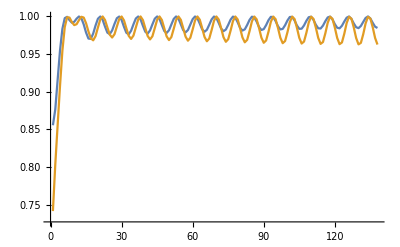

```mathematica
ListPlot[{Wp,Wm},Joined->True,PlotRange->All]
```

### Static simulation

#### Simulation

```mathematica
(*Preample*)
{dt,n,T}={0.5,100,100}; 
{J,k}={40,-42};   
{Ex,Eθ} = {0,0};
{b1,b2} = {1,1};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs}={{},{}};
{Wps,Wms}={{},{}};
ts={};

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
{Wp,Wm}=findWs[znew];AppendTo[ts,dt*t];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
]
```

#### Plots

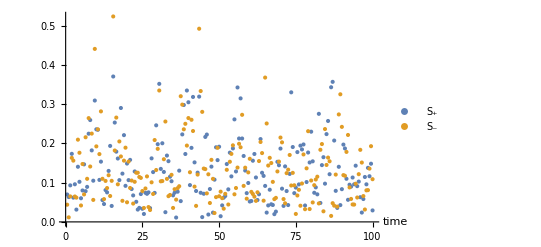

```mathematica
ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"S_+","S_-"}]
```

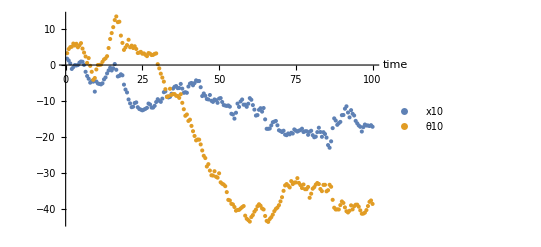

```mathematica
swarmalatorIndex=10;
ListPlot[{{ts,xs[[All,swarmalatorIndex]]}ᵀ,{ts,θs[[All,swarmalatorIndex]]}ᵀ},AxesLabel->{Style["time",13]},
PlotLegends->{"x"<>ToString[swarmalatorIndex],"θ"<>ToString[swarmalatorIndex]}]
```

```mathematica
(*Manipulate[ListPlot[{xs[[t,All]]//mod,θs[[t,All]]//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}],{t,1,Dimensions[xs][[2]],1}]*)
```

## Compare to magnetic domain walls

### Method

```mathematica
plotResults1[z_]:=Block[{colors,Wp,Wm,p1,p2,p3,p4,p5,x,θ,xin,θin},
{x,θ}={z[[1,All]],z[[2,All]]};

{xin,θin}={pin[[1,All]],pin[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];

p2=Graphics[{PointSize[0.05],Point[{Mod[x[[1]],2π],Mod[x[[2]],2π]}]},Axes->True,PlotRange->{{0,2π},{0,2π}},AxesLabel->{"x1","x2"},LabelStyle->15,ImageSize->Medium];
p3=Graphics[{PointSize[0.05],Point[{Sin[θ[[1]]],Sin[θ[[2]]]}]},Axes->True,PlotRange->{{-1.1,1.1},{-1.1,1.1}},AxesLabel->{"Sin θ1","Sinθ2"},LabelStyle->15,ImageSize->Medium];
Return[Grid[{{p1,p2,p3}}]]
];
```

### Movie

#### Traveling loops

```mathematica
(*Preamble*)
{dt,n,T}={0.1,2,100}; 
{J,k,b,e}={1,10,0.5,0.2};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{1.5π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
If[n==2,pin={{0,π},{0,π}}];
z00 = z0;
results={};
Dynamic[results] (*For dynamic plotting*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
sols={};
ts={};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;AppendTo[sols,znew];AppendTo[ts,t*dt];
results=plotResults1[znew]
]
```

```mathematica
Length[ts]
```

1000

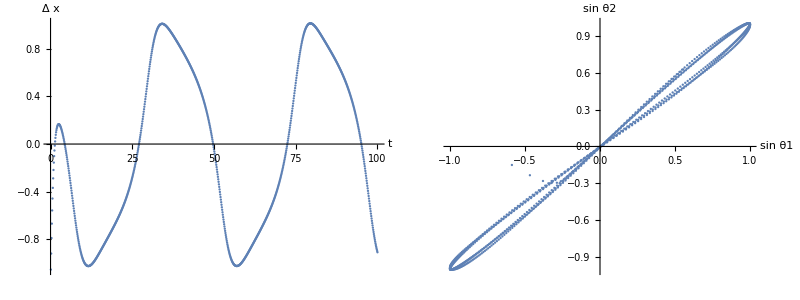

```mathematica
{x,θ}=znew;
{x1,x2}={sols[[All,1,1]],sols[[All,1,2]]};
{θ1,θ2}={sols[[All,2,1]],sols[[All,2,2]]};
p1=ListPlot[{ts,x1-x2}ᵀ,AxesLabel->{"t","Δ x"},LabelStyle->15,ImageSize->Medium];
p2=ListPlot[{Sin[θ1],Sin[θ2]}ᵀ,AxesLabel->{"sin θ1"," sin θ2"},LabelStyle->15,ImageSize->Medium];
Grid[{{p1,p2}}]
```

#### Static phase wave

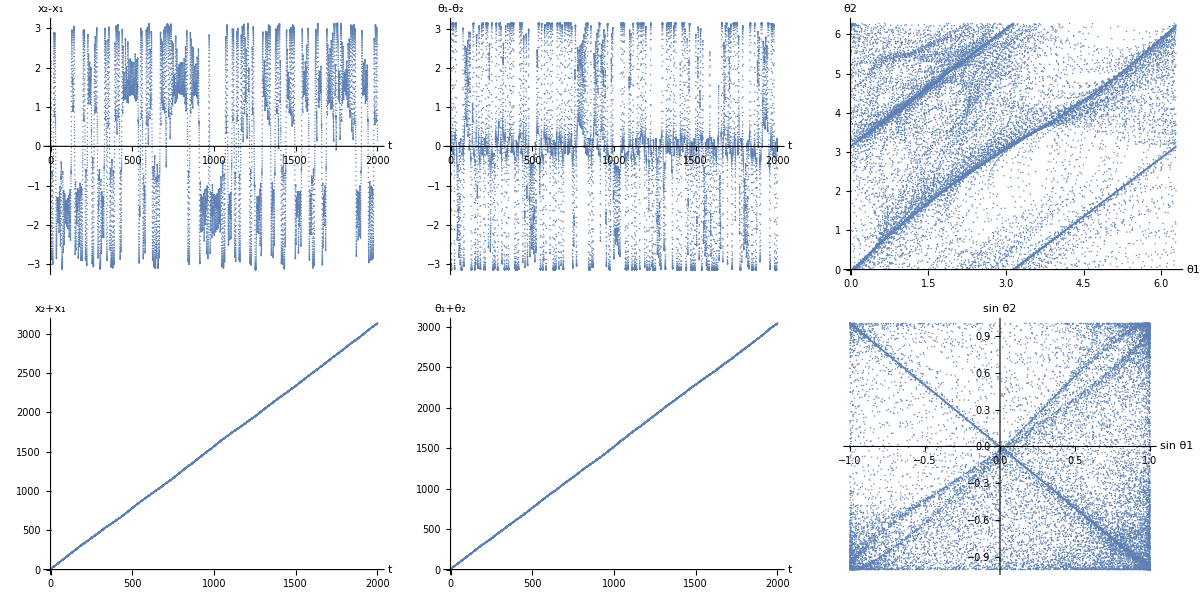

```mathematica
(*Preamble*)
{dt,n,T}={0.1,2,2000}; 
{J,k,b,e}={1,-5,0.5,0.9};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{1.5π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
If[n==2,pin={{0,π},{0,π}}];
z00 = z0;
results={};
Dynamic[results] (*For dynamic plotting*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
sols={};
ts={};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;AppendTo[sols,znew];AppendTo[ts,t*dt];
results=plotResults1[znew]
]

{x,θ}=znew;
{x1,x2}={sols[[All,1,1]],sols[[All,1,2]]};
{θ1,θ2}={sols[[All,2,1]],sols[[All,2,2]]};
p1=ListPlot[{ts,x1-x2}ᵀ,AxesLabel->{"t","x_2-x_1"},LabelStyle->15,ImageSize->Medium];
p2=ListPlot[{ts,x1+x2}ᵀ,AxesLabel->{"t","x_2+x_1"},LabelStyle->15,ImageSize->Medium];
p3=ListPlot[{ts,θ1-θ2}ᵀ,AxesLabel->{"t","θ_1-θ_2"},LabelStyle->15,ImageSize->Medium];
p4=ListPlot[{ts,θ1+θ2}ᵀ,AxesLabel->{"t","θ_1+θ_2"},LabelStyle->15,ImageSize->Medium];
p5=ListPlot[{Mod[θ1,2π],Mod[θ2,2π]}ᵀ,AxesLabel->{"θ1"," θ2"},LabelStyle->15,ImageSize->Medium,PlotRange->{{0,2π},{0,2π}}];
p6=ListPlot[{Sin[θ1],Sin[θ2]}ᵀ,AxesLabel->{"sin θ1"," sin θ2"},LabelStyle->15,ImageSize->Medium,PlotRange->{{-1,1},{-1,1}}];
Grid[{{p1,p3,p5},{p2,p4,p6}}]
```

Very interesing! Is this chaos??

## Chaos?

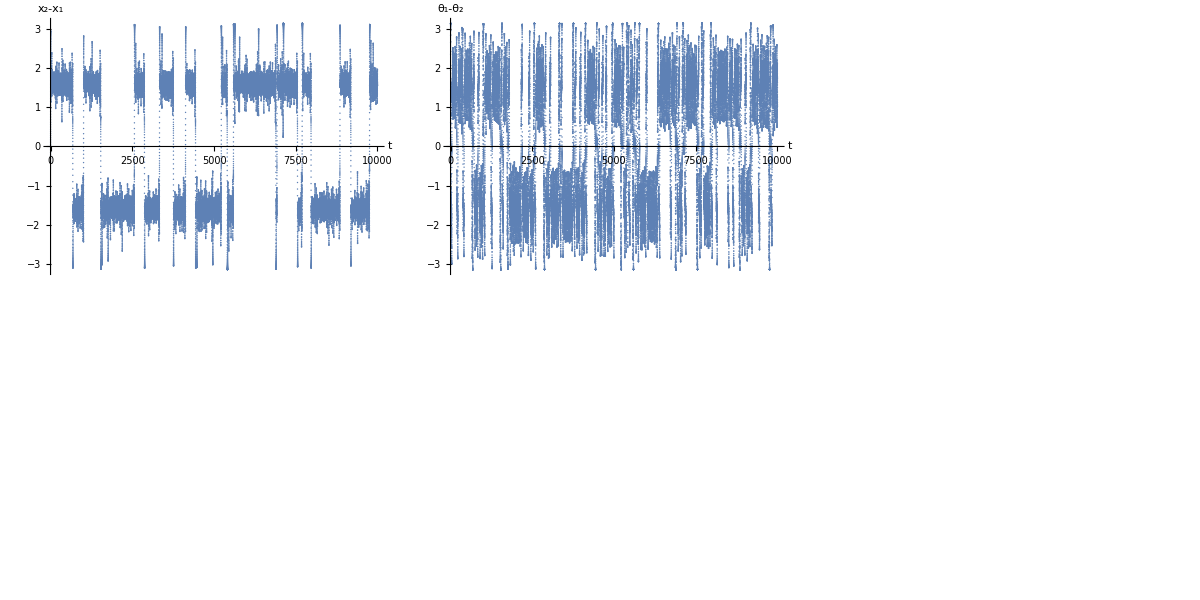

```mathematica
(*Preamble*)
{dt,n,T}={0.1,2,10000}; 
{J,k,b,e}={1,-5,0.5,0.39};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{1.5π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
If[n==2,pin={{0,π},{0,π}}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
sols={};
ts={};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;AppendTo[sols,znew];AppendTo[ts,t*dt];
]

{x,θ}=znew;
{x1,x2}={sols[[All,1,1]],sols[[All,1,2]]};
{θ1,θ2}={sols[[All,2,1]],sols[[All,2,2]]};
p1=ListPlot[{ts,x1-x2}ᵀ,AxesLabel->{"t","x_2-x_1"},LabelStyle->15,ImageSize->Medium];
p2=ListPlot[{ts,x1+x2}ᵀ,AxesLabel->{"t","x_2+x_1"},LabelStyle->15,ImageSize->Medium];
p3=ListPlot[{ts,θ1-θ2}ᵀ,AxesLabel->{"t","θ_1-θ_2"},LabelStyle->15,ImageSize->Medium];
p4=ListPlot[{ts,θ1+θ2}ᵀ,AxesLabel->{"t","θ_1+θ_2"},LabelStyle->15,ImageSize->Medium];
p5=ListPlot[{Mod[θ1,2π],Mod[θ2,2π]}ᵀ,AxesLabel->{"θ1"," θ2"},LabelStyle->15,ImageSize->Medium,PlotRange->{{0,2π},{0,2π}}];
p6=ListPlot[{Sin[θ1],Sin[θ2]}ᵀ,AxesLabel->{"sin θ1"," sin θ2"},LabelStyle->15,ImageSize->Medium,PlotRange->{{-1,1},{-1,1}}];
Grid[{{p1,p3,p5},{p2,p4,p6}}]
```

### Limit cycle

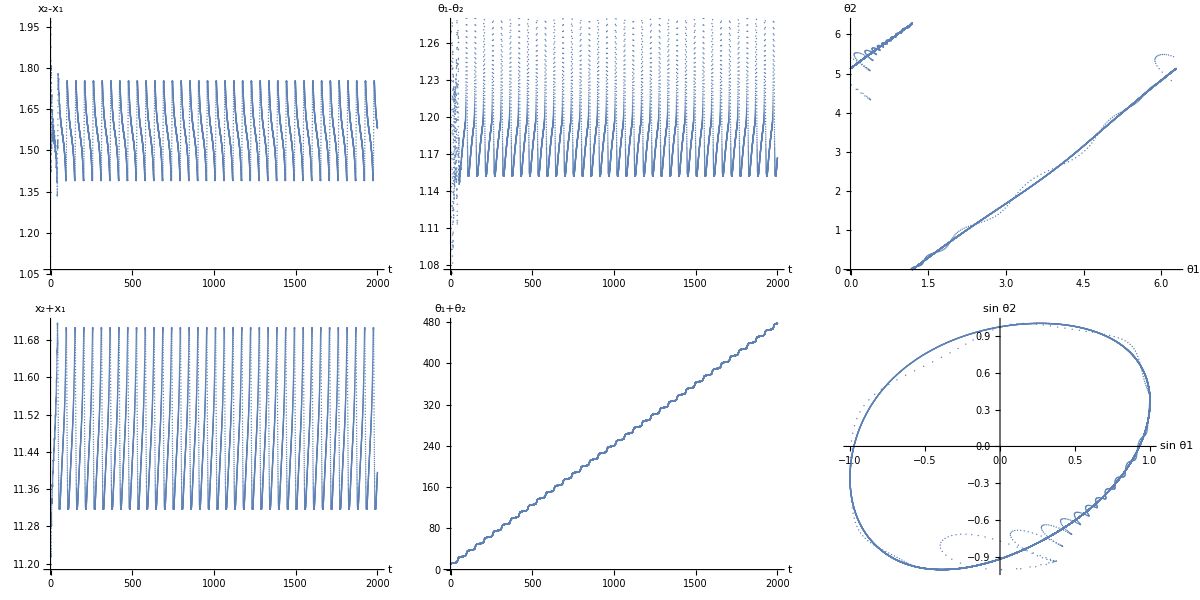

```mathematica
(*Preamble*)
{dt,n,T}={0.1,2,2000}; 
{J,k,b,e}={1,-5,0.5,0.3};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{1.5π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
If[n==2,pin={{0,π},{0,π}}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
sols={};
ts={};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;AppendTo[sols,znew];AppendTo[ts,t*dt];
]

{x,θ}=znew;
{x1,x2}={sols[[All,1,1]],sols[[All,1,2]]};
{θ1,θ2}={sols[[All,2,1]],sols[[All,2,2]]};
p1=ListPlot[{ts,x1-x2}ᵀ,AxesLabel->{"t","x_2-x_1"},LabelStyle->15,ImageSize->Medium];
p2=ListPlot[{ts,x1+x2}ᵀ,AxesLabel->{"t","x_2+x_1"},LabelStyle->15,ImageSize->Medium];
p3=ListPlot[{ts,θ1-θ2}ᵀ,AxesLabel->{"t","θ_1-θ_2"},LabelStyle->15,ImageSize->Medium];
p4=ListPlot[{ts,θ1+θ2}ᵀ,AxesLabel->{"t","θ_1+θ_2"},LabelStyle->15,ImageSize->Medium];
p5=ListPlot[{Mod[θ1,2π],Mod[θ2,2π]}ᵀ,AxesLabel->{"θ1"," θ2"},LabelStyle->15,ImageSize->Medium,PlotRange->{{0,2π},{0,2π}}];
p6=ListPlot[{Sin[θ1],Sin[θ2]}ᵀ,AxesLabel->{"sin θ1"," sin θ2"},LabelStyle->15,ImageSize->Medium,PlotRange->{{-1,1},{-1,1}}];
Grid[{{p1,p3,p5},{p2,p4,p6}}]
```

### Period doupling

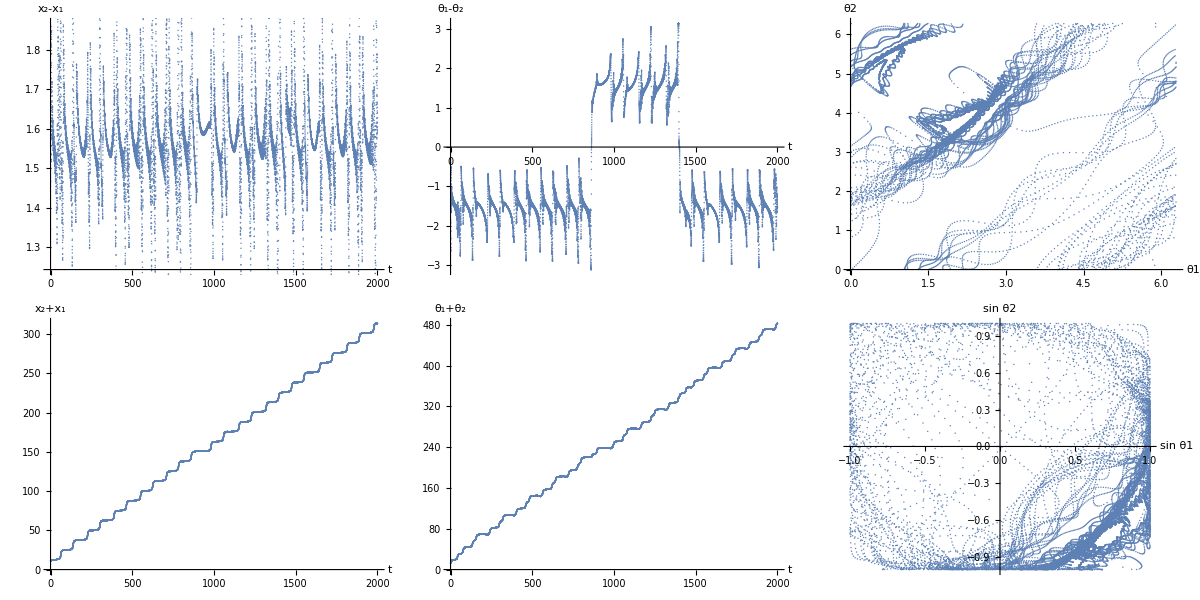

```mathematica
(*Preamble*)
{dt,n,T}={0.1,2,2000}; 
{J,k,b,e}={1,-5,0.5,0.36};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{1.5π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
If[n==2,pin={{0,π},{0,π}}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
sols={};
ts={};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;AppendTo[sols,znew];AppendTo[ts,t*dt];
]

{x,θ}=znew;
{x1,x2}={sols[[All,1,1]],sols[[All,1,2]]};
{θ1,θ2}={sols[[All,2,1]],sols[[All,2,2]]};
p1=ListPlot[{ts,x1-x2}ᵀ,AxesLabel->{"t","x_2-x_1"},LabelStyle->15,ImageSize->Medium];
p2=ListPlot[{ts,x1+x2}ᵀ,AxesLabel->{"t","x_2+x_1"},LabelStyle->15,ImageSize->Medium];
p3=ListPlot[{ts,θ1-θ2}ᵀ,AxesLabel->{"t","θ_1-θ_2"},LabelStyle->15,ImageSize->Medium];
p4=ListPlot[{ts,θ1+θ2}ᵀ,AxesLabel->{"t","θ_1+θ_2"},LabelStyle->15,ImageSize->Medium];
p5=ListPlot[{Mod[θ1,2π],Mod[θ2,2π]}ᵀ,AxesLabel->{"θ1"," θ2"},LabelStyle->15,ImageSize->Medium,PlotRange->{{0,2π},{0,2π}}];
p6=ListPlot[{Sin[θ1],Sin[θ2]}ᵀ,AxesLabel->{"sin θ1"," sin θ2"},LabelStyle->15,ImageSize->Medium,PlotRange->{{-1,1},{-1,1}}];
Grid[{{p1,p3,p5},{p2,p4,p6}}]
```

### Stuff here

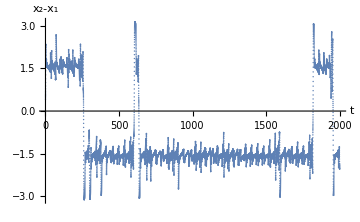
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
(*Preamble*)
{dt,n,T}={0.1,2,2000}; 
{J,k,b,e}={1,-5,0.5,0.39};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{1.5π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
If[n==2,pin={{0,π},{0,π}}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
sols={};
ts={};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;AppendTo[sols,znew];AppendTo[ts,t*dt];
]

{x,θ}=znew;
{x1,x2}={sols[[All,1,1]],sols[[All,1,2]]};
{θ1,θ2}={sols[[All,2,1]],sols[[All,2,2]]};
p1=ListPlot[{ts,x1-x2}ᵀ,AxesLabel->{"t","x_2-x_1"},LabelStyle->15,ImageSize->Medium];
p2=ListPlot[{ts,x1+x2}ᵀ,AxesLabel->{"t","x_2+x_1"},LabelStyle->15,ImageSize->Medium];
p3=ListPlot[{ts,θ1-θ2}ᵀ,AxesLabel->{"t","θ_1-θ_2"},LabelStyle->15,ImageSize->Medium];
p4=ListPlot[{ts,θ1+θ2}ᵀ,AxesLabel->{"t","θ_1+θ_2"},LabelStyle->15,ImageSize->Medium];
p5=ListPlot[{Mod[θ1,2π],Mod[θ2,2π]}ᵀ,AxesLabel->{"θ1"," θ2"},LabelStyle->15,ImageSize->Medium,PlotRange->{{0,2π},{0,2π}}];
p6=ListPlot[{Sin[θ1],Sin[θ2]}ᵀ,AxesLabel->{"sin θ1"," sin θ2"},LabelStyle->15,ImageSize->Medium,PlotRange->{{-1,1},{-1,1}}];
Grid[{{p1,p3,p5},{p2,p4,p6}}]
```

## S_±(K) -- numerically

### E = 0

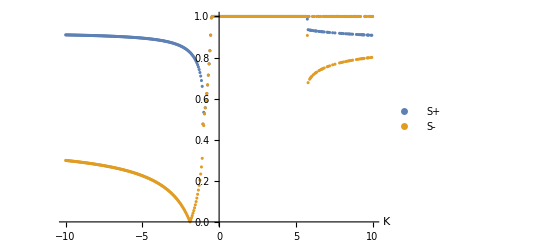

```mathematica
data=ParallelTable[
{dt,n,T}={0.1,2,200}; 
{J,k}={1,k1};
{e,b}={0,0.5};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
If[n==2,pin={{0,π},{0,π}}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k1,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.5Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{k1,Sp,Sm},
{k1,-10,10,0.05}
];
ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},AxesLabel->{"K"},PlotLegends->{"S+","S-"},AxesStyle->15,PlotStyle->All]
```

Looks like there’s bistability there for K > 5 ish.

### E > 0

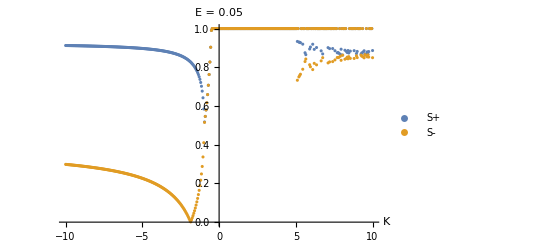

```mathematica
data=ParallelTable[
{dt,n,T}={0.1,2,200}; 
{J,k}={1,k1};
{e,b}={0.05,0.5};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
If[n==2,pin={{0,π},{0,π}}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k1,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.5Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{k1,Sp,Sm},
{k1,-10,10,0.05}
];
ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},AxesLabel->{"K"},PlotLegends->{"S+","S-"},AxesStyle->15,PlotStyle->All,PlotLabel->"E = 0.05"]
```

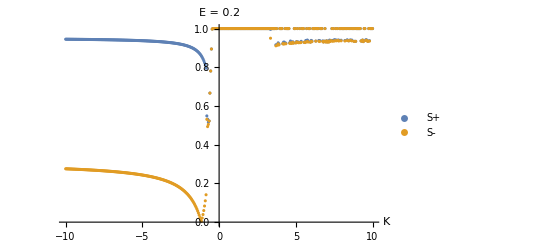

```mathematica
data=ParallelTable[
{dt,n,T}={0.1,2,200}; 
{J,k}={1,k1};
{e,b}={0.2,0.5};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
If[n==2,pin={{0,π},{0,π}}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k1,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.5Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{k1,Sp,Sm},
{k1,-10,10,0.05}
];
ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},AxesLabel->{"K"},PlotLegends->{"S+","S-"},AxesStyle->15,PlotStyle->All,PlotLabel->"E = 0.2"]
```

Looks like there’s bistability

## Analysis: original (x1,x2,t1,t2) coords

### Find fp when E = 0

```mathematica
Clear[e,b,k]
v={
e-b Sin[x1-α1]+j/2 Sin[x2-x1]Cos[θ2-θ1],
e-b Sin[x2-α2]-j/2 Sin[x2-x1]Cos[θ2-θ1],
e-b Sin[θ1-α1]+k/2 Sin[θ2-θ1]Cos[x2-x1],
e-b Sin[θ2-α2]-k/2 Sin[θ2-θ1]Cos[x1-x2]
}/.{α1->0,α2->π,e->0};
TableForm[v]
```

-b Sin[x1]-1/2 j Cos[θ1-θ2] Sin[x1-x2]
1/2 j Cos[θ1-θ2] Sin[x1-x2]+b Sin[x2]
-b Sin[θ1]-1/2 k Cos[x1-x2] Sin[θ1-θ2]
1/2 k Cos[x1-x2] Sin[θ1-θ2]+b Sin[θ2]

```mathematica
fp=Solve[(v/.α1->0/.α2->π/.j->1/.b->0.5)=={0,0,0,0},{x1,x2,θ1,θ2}];
Length[fp]
TableForm[fp]
```

$Aborted

0

{}

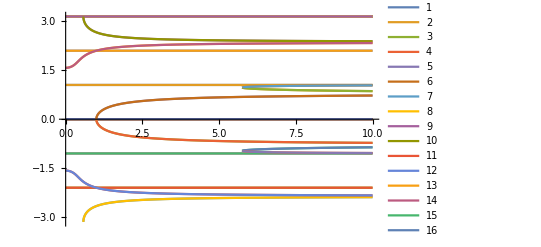

```mathematica
Plot[x1/.fp/.b->0.5/.k->k1/.C[1]->0/.C[2]->0//Evaluate,{k1,0,10},PlotLegends->Table[i,{i,1,Length[fp]}]]
```

```mathematica
FullSimplify[{x1,x2,θ1,θ2}/.fp[[48;;52]]/.C[1]->0/.C[2]->0/.C[3]->0/.C[4]->0]//TableForm
```

1
 |  |  |  |

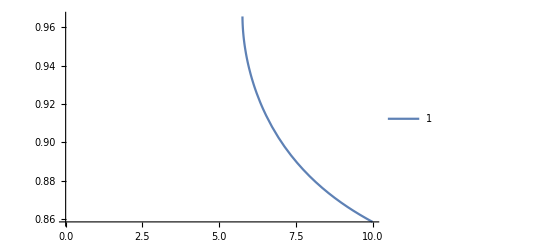

```mathematica
Plot[x1/.fp[[48]]/.b->0.5/.k->k1/.C[1]->0/.C[2]->0//Evaluate,{k1,0,10},PlotLegends->Table[i,{i,1,Length[fp]}]]
```

```mathematica
temp=FullSimplify[x1/.fp[[48]]/.C[1]->0]
```

ArcTan[k^2-b^2 (2+k^2)+Root[-4 b^4+4 b^2 k^2-k^4+b^2 k^4+(4 b^4-20 b^2 k^2+9 k^4-8 b^2 k^4) #1+(32 b^2 k^2-32 k^4+24 b^2 k^4) #1^2+(-16 b^2 k^2+56 k^4-32 b^2 k^4) #1^3+(-48 k^4+16 b^2 k^4) #1^4+16 k^4 #1^5&,4] (-5 k^2+b^2 (2+4 k^2)-4 k^2 Root[-4 b^4+4 b^2 k^2-k^4+b^2 k^4+(4 b^4-20 b^2 k^2+9 k^4-8 b^2 k^4) #1+(32 b^2 k^2-32 k^4+24 b^2 k^4) #1^2+(-16 b^2 k^2+56 k^4-32 b^2 k^4) #1^3+(-48 k^4+16 b^2 k^4) #1^4+16 k^4 #1^5&,4] (-2+b^2+Root[-4 b^4+4 b^2 k^2-k^4+b^2 k^4+(4 b^4-20 b^2 k^2+9 k^4-8 b^2 k^4) #1+(32 b^2 k^2-32 k^4+24 b^2 k^4) #1^2+(-16 b^2 k^2+56 k^4-32 b^2 k^4) #1^3+(-48 k^4+16 b^2 k^4) #1^4+16 k^4 #1^5&,4])),2 b^3 √Root[-4 b^4+4 b^2 k^2-k^4+b^2 k^4+(4 b^4-20 b^2 k^2+9 k^4-8 b^2 k^4) #1+(32 b^2 k^2-32 k^4+24 b^2 k^4) #1^2+(-16 b^2 k^2+56 k^4-32 b^2 k^4) #1^3+(-48 k^4+16 b^2 k^4) #1^4+16 k^4 #1^5&,4]]

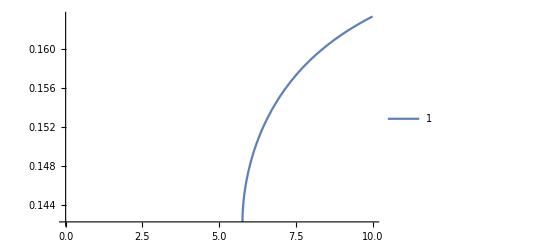

```mathematica
Plot[temp[[1]]/.b->0.5/.k->k1/.C[1]->0/.C[2]->0//Evaluate,{k1,0,10},PlotLegends->Table[i,{i,1,Length[fp]}]]
```

```mathematica
f[k_,b_]:=Evaluate[temp[[1]]]
```

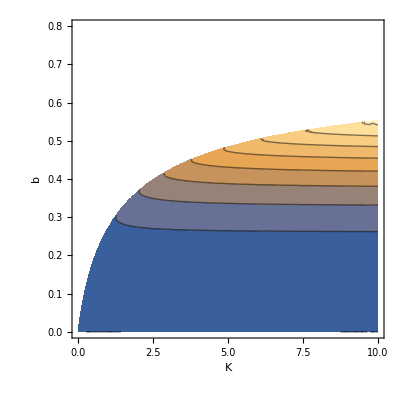

```mathematica
ContourPlot[f[k,b],{k,0,10},{b,0,0.8},FrameLabel->{Style["K",15,Italic],Style["b",15,Italic]}]
```

This is when the static phase wave destabilizes?

### Turn E = 0 on

```mathematica
Clear[e,b,k]
v={
e-b Sin[x1-α1]+j/2 Sin[x2-x1]Cos[θ2-θ1],
e-b Sin[x2-α2]-j/2 Sin[x2-x1]Cos[θ2-θ1],
e-b Sin[θ1-α1]+k/2 Sin[θ2-θ1]Cos[x2-x1],
e-b Sin[θ2-α2]-k/2 Sin[θ2-θ1]Cos[x1-x2]
}/.{α1->0,α2->π,b->1,j->k};
TableForm[v]
```

e-Sin[x1]-1/2 k Cos[θ1-θ2] Sin[x1-x2]
e+1/2 k Cos[θ1-θ2] Sin[x1-x2]+Sin[x2]
e-Sin[θ1]-1/2 k Cos[x1-x2] Sin[θ1-θ2]
e+1/2 k Cos[x1-x2] Sin[θ1-θ2]+Sin[θ2]

```mathematica
fp=Solve[(v/.e->0)=={0,0,0,0},{x1,x2,θ1,θ2}];
Length[fp]
TableForm[fp]
```

52

1
 |  |  |  |

```mathematica
subC=C[1]->0/.C[2]->0/.C[3]->0/.C[4]->0/.C[5]->0;
Plot[x1/.fp/.subC/.k->k1,{k1,0,10},PlotLegends->Table[i,{i,1,Length[fp]}]]
```

-Graphics-

```mathematica
subC=C[1]->0/.C[2]->0/.C[3]->0/.C[4]->0/.C[5]->0;
Plot[x1/.fp[[25;;30]]/.subC/.k->k1,{k1,0,10}]
```

-Graphics-

```mathematica
x1/.fp[[25]]
```

ConditionalExpression[ArcTan[-1/k,-(√(-1+k^2))/k]+2 π C[1], C[1]∈ℤ]

#### Solve numerically warm up

```mathematica
Clear[e,b,k,t];

(*SeedRandom[0];*)
odes={
x1'[t]==e-b Sin[x1[t]-α1]+j/2 Sin[x2[t]-x1[t]]Cos[θ2[t]-θ1[t]],
x2'[t]==e-b Sin[x2[t]-α2]-j/2 Sin[x2[t]-x1[t]]Cos[θ2[t]-θ1[t]],
θ1'[t]==e-b Sin[θ1[t]-α1]+k/2 Sin[θ2[t]-θ1[t]]Cos[x2[t]-x1[t]],
θ2'[t]==e-b Sin[θ2[t]-α2]-k/2 Sin[θ2[t]-θ1[t]]Cos[x1[t]-x2[t]]
}/.{α1->0,α2->π};

ics={x1[0]==RandomReal[{-π,π}],x2[0]==RandomReal[{-π,π}],θ1[0]==RandomReal[{-π,π}],θ2[0]==RandomReal[{-π,π}]};

fns={x1[t],x2[t],θ1[t],θ2[t]};

{k1,e1,T}={6,0,100};
subs={j->k1,k->k1,b->1,e->e1};
sols=NDSolve[{odes/.subs,ics},fns,{t,0,T}];

Plot[fns/.sols//Evaluate,{t,0,T},PlotLegends->fns,PlotLabel->"{K,E} = "<>ToString[{k1,e1}],LabelStyle->15,PlotRange->{-π,π}]
```

-Graphics-

```mathematica
x1[t]/.sols/.t->T
```

{1.39191}

```mathematica
x1/.fp/.k->6/.C[1]->0/.C[2]->0/.C[3]->0/.C[4]->0//N//TableForm
```

0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
3.14159
3.14159
3.14159
3.14159
3.14159
3.14159
3.14159
3.14159
3.14159
3.14159
3.14159
3.14159
-1.73824
-1.73824
1.73824
1.73824
-1.40335
-1.40335
1.40335
1.40335
-2.25063
-2.25063
2.25063
2.25063
-0.651239
-0.651239
0.651239
0.651239
-1.39191+3.24746×10^-16 ⅈ
-1.39191+3.24746×10^-16 ⅈ
1.39191-3.24746×10^-16 ⅈ
1.39191-3.24746×10^-16 ⅈ
-0.925863-1.55431×10^-15 ⅈ
-0.925863-1.55431×10^-15 ⅈ
0.925863+1.55431×10^-15 ⅈ
0.925863+1.55431×10^-15 ⅈ
-2.46399-8.88178×10^-16 ⅈ
-2.46399-8.88178×10^-16 ⅈ
2.46399+8.88178×10^-16 ⅈ
2.46399+8.88178×10^-16 ⅈ

```mathematica
x1/.fp[[-12]]/.k->6//N
```

ConditionalExpression[(-1.39191+3.24746×10^-16 ⅈ)+6.28319 C[1], C[1]∈ℤ]

```mathematica
FullSimplify[x1/.fp[[-12]]]/.C[1]->0
```

ArcTan[((-9 k^4+√(81 k^8-6 k^10)) (k^2-(-27 k^4+k^6+3 √(81 k^8-6 k^10))^(1/3)))/(k^3 (-27 k^4+k^6+3 √(81 k^8-6 k^10))^(2/3)),-√6 √(4+k^2/((-27 k^4+k^6+3 √(81 k^8-6 k^10))^(1/3))+((-27 k^4+k^6+3 √(81 k^8-6 k^10))^(1/3))/k^2)]

```mathematica
P
```

```mathematica
solve[k_,e_]:=Module[{odes,ics,fns,k1,e1,t,T,subs,sols},
odes={
x1'[t]==e-b Sin[x1[t]-α1]+j/2 Sin[x2[t]-x1[t]]Cos[θ2[t]-θ1[t]],
x2'[t]==e-b Sin[x2[t]-α2]-j/2 Sin[x2[t]-x1[t]]Cos[θ2[t]-θ1[t]],
θ1'[t]==e-b Sin[θ1[t]-α1]+k/2 Sin[θ2[t]-θ1[t]]Cos[x2[t]-x1[t]],
θ2'[t]==e-b Sin[θ2[t]-α2]-k/2 Sin[θ2[t]-θ1[t]]Cos[x1[t]-x2[t]]
}/.{α1->0,α2->π};

ics={x1[0]==RandomReal[{-π,π}],x2[0]==RandomReal[{-π,π}],θ1[0]==RandomReal[{-π,π}],θ2[0]==RandomReal[{-π,π}]};

fns={x1[t],x2[t],θ1[t],θ2[t]};

{k1,e1,T}={2,0,10};
subs={j->k1,k->k1,b->1,e->e1};
sols=NDSolve[{odes/.subs,ics},fns,{t,0,T}];

Return[{fns/.sols/.t->T,k,e}]
]
```

```mathematica
solve[1,1]
```

NDSolve::ndnco: The number of constraints (4) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (8).

ReplaceAll::reps: {NDSolve[{{x1''[t$294923]==2-Sin[«1»]-Cos[«1»] Sin[«1»],x2''[t$294923]==2+Cos[«1»] Sin[«1»]+Sin[x2[«1»]],θ1''[t$294923]==2-Sin[«1»]-1/2 Cos[«1»] Sin[«1»],θ2''[t$294923]==2+1/2 Cos[«1»] Sin[«1»]+Sin[θ2[«1»]]},{x1[0]==2.54334,x2[0]==0.884122,θ1[0]==-1.21555,θ2[0]==1.60974}},{x1[t$294923],x2[t$294923],θ1[t$294923],θ2[t$294923]},{t$294923,0,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 10 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{x1''[10]==2-Sin[«1»]-Cos[«1»] Sin[«1»],x2''[10]==2+Cos[«1»] Sin[«1»]+Sin[x2[«1»]],θ1''[10]==2-Sin[«1»]-1/2 Cos[«1»] Sin[«1»],θ2''[10]==2+1/2 Cos[«1»] Sin[«1»]+Sin[θ2[«1»]]},{x1[0]==2.54334,x2[0]==0.884122,θ1[0]==-1.21555,θ2[0]==1.60974}},{x1[10],x2[10],θ1[10],θ2[10]},{10,0,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{{x1[10],x2[10],θ1[10],θ2[10]}/.NDSolve[{{x1''[10]==2-Sin[x1[10]]-Cos[θ1[10]-θ2[10]] Sin[x1[10]-x2[10]],x2''[10]==2+Cos[θ1[10]-θ2[10]] Sin[x1[10]-x2[10]]+Sin[x2[10]],θ1''[10]==2-Sin[θ1[10]]-1/2 Cos[x1[10]-x2[10]] Sin[θ1[10]-θ2[10]],θ2''[10]==2+1/2 Cos[x1[10]-x2[10]] Sin[θ1[10]-θ2[10]]+Sin[θ2[10]]},{x1[0]==2.54334,x2[0]==0.884122,θ1[0]==-1.21555,θ2[0]==1.60974}},{x1[10],x2[10],θ1[10],θ2[10]},{10,0,10}],1,1}

#### Numerical fixed point

```mathematica
data=ParallelTable[
SeedRandom[2];
odes={
x1'[t]==e-b Sin[x1[t]-α1]+j/2 Sin[x2[t]-x1[t]]Cos[θ2[t]-θ1[t]],
x2'[t]==e-b Sin[x2[t]-α2]-j/2 Sin[x2[t]-x1[t]]Cos[θ2[t]-θ1[t]],
θ1'[t]==e-b Sin[θ1[t]-α1]+k/2 Sin[θ2[t]-θ1[t]]Cos[x2[t]-x1[t]],
θ2'[t]==e-b Sin[θ2[t]-α2]-k/2 Sin[θ2[t]-θ1[t]]Cos[x1[t]-x2[t]]
}/.{α1->0,α2->π};

ics={x1[0]==RandomReal[{-π,π}],x2[0]==RandomReal[{-π,π}],θ1[0]==RandomReal[{-π,π}],θ2[0]==RandomReal[{-π,π}]};

fns={x1[t],x2[t],θ1[t],θ2[t]};

{e1,T}={0,10};
subs={j->k1,k->k1,b->1,e->e1};
sols=NDSolve[{odes/.subs,ics},fns,{t,0,T}];
{fns/.sols/.t->T,k1,e1}//Flatten,
{k1,0,10,0.05}
];
```

```mathematica
p1=ListPlot[{data[[All,{5,1}]],data[[All,{5,2}]],data[[All,{5,3}]],data[[All,{5,4}]]}//Evaluate,AxesLabel->{Style["K",Italic]},PlotLegends->fns,LabelStyle->15,PlotLabel->"E = "<>ToString[e1]]
```

-Graphics-

```mathematica
subC=C[1]->0/.C[2]->0/.C[3]->0/.C[4]->0/.C[5]->0;
Plot[x1/.fp/.subC/.k->k1,{k1,0,10},PlotLegends->Table[i,{i,1,Length[fp]}]]
```

-Graphics-

```mathematica
p1=ListPlot[{data[[All,{5,1}]],data[[All,{5,2}]],data[[All,{5,3}]],data[[All,{5,4}]]},AxesLabel->{Style["K",Italic]},PlotLegends->fns,LabelStyle->15,PlotLabel->"E = "<>ToString[e1],PlotRange->{-π,π},Joined->True];
p2=Plot[x1/.fp[[1;;52]]/.subC/.k->k1,{k1,0,10},PlotStyle->{Black,Dashed}];
Show[{p1,p2}]
```

$Aborted

-Graphics-

```mathematica
p1=ListPlot[{data[[All,{5,1}]],data[[All,{5,2}]],data[[All,{5,3}]],data[[All,{5,4}]]},AxesLabel->{Style["K",Italic]},PlotLegends->fns,LabelStyle->15,PlotLabel->"E = "<>ToString[e1],PlotRange->{-π,π},Joined->True];
p2=Plot[-ArcTan[((-9 k^4+√(81 k^8-6 k^10)) (k^2-(-27 k^4+k^6+3 √(81 k^8-6 k^10))^(1/3)))/(k^3 (-27 k^4+k^6+3 √(81 k^8-6 k^10))^(2/3)),-√6 √(4+k^2/((-27 k^4+k^6+3 √(81 k^8-6 k^10))^(1/3))+((-27 k^4+k^6+3 √(81 k^8-6 k^10))^(1/3))/k^2)],{k,0,10},PlotStyle->{Black,Dashed}];
Show[{p1,p2}]
```

-Graphics-

## Bifucations

### x = const etc

```mathematica
Clear[e,b,k]
es={
e-b Sin[x1-α1]+j/2 Sin[x2-x1]Cos[θ2-θ1],
e-b Sin[x2-α2]-j/2 Sin[x2-x1]Cos[θ2-θ1],
e-b Sin[θ1-α1]+k/2 Sin[θ2-θ1]Cos[x2-x1],
e-b Sin[θ2-α2]-k/2 Sin[θ2-θ1]Cos[x1-x2]
}/.{α1->0,α2->π,b->1,j->k};
TableForm[v]
```

```mathematica
fp=Solve[(es/.e->0)==0,{x1,x2,θ1,θ2}];
TableForm[fp]
```

1
 |  |  |  |

#### λ(k) for a bunch of FP

```mathematica
figs=ParallelTable[
J={D[es, x1],D[es, x2],D[es, θ1],D[es, θ2]};
λ=Eigenvalues[J/.fp[[i]]/.C[1]->0/.C[2]->0/.C[3]->0/.C[4]->0];
Plot[λ//Evaluate,{k,0,5},PlotLabel->"i = "<>ToString[i],LabelStyle->15,AxesOrigin->{0,0}],
{i,1,40}
];
Grid[Partition[figs,UpTo[8]]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
i=8;
J={D[es, x1],D[es, x2],D[es, θ1],D[es, θ2]};
λ=Eigenvalues[J/.fp[[i]]/.C[1]->0/.C[2]->0/.C[3]->0/.C[4]->0]
Plot[λ//Evaluate,{k,0,5},PlotLabel->"i = "<>ToString[i],LabelStyle->15,AxesOrigin->{0,0}]
```

{-1,-1,-1-k,-1-k}

-Graphics-

```mathematica
subC={C[1]->0,C[2]->0,C[3]->0,C[4]->0};
fp[[8]]/.subC/.subC
```

{x1→0,x2→-π,θ1→0,θ2→-π}

So this is the pinned state?  Stable for all k. Interesting

```mathematica
figs=ParallelTable[
J={D[es, x1],D[es, x2],D[es, θ1],D[es, θ2]};
λ=Eigenvalues[J/.fp[[i]]/.C[1]->0/.C[2]->0/.C[3]->0/.C[4]->0];
Plot[λ//Re//Evaluate,{k,0,10},PlotLabel->"i = "<>ToString[i],LabelStyle->15,AxesOrigin->{0,0}],
{i,1,40}
];
Grid[Partition[figs,UpTo[8]]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

#### Harder fixed points

```mathematica
J1=TrigExpand[J]/.fp[[41]]/.subC//Simplify;
λ=Table[Eigenvalues[J1/.k->k1//N],{k1,0.1,10,0.1}]//Chop;
ListPlot[{λ[[All,1]],λ[[All,2]],λ[[All,3]],λ[[All,4]]}]
```

-Graphics-

```mathematica
J1=TrigExpand[J]/.fp[[49]]/.subC//Simplify;
λ=Table[Eigenvalues[J1/.k->k1//N],{k1,0.1,10,0.1}]//Chop;
ListPlot[{λ[[All,1]],λ[[All,2]],λ[[All,3]],λ[[All,4]]}]
```

Power::infy: Infinite expression 1/0. encountered.

Eigenvalues::inf: Input matrix contains an infinite entry.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Eigenvalues::inf: Input matrix contains an infinite entry.

General::stop: Further output of Eigenvalues::inf will be suppressed during this calculation.

Part::partw: Part 2 of Eigenvalues[{{ComplexInfinity,1.14197-1.55975×10^-8 ⅈ,-1.04177-8.84681×10^-7 ⅈ,1.04177+8.84681×10^-7 ⅈ},{1.14197-1.55975×10^-8 ⅈ,ComplexInfinity,1.04177+8.84681×10^-7 ⅈ,-1.04177-8.84681×10^-7 ⅈ},{-1.04177-8.84681×10^-7 ⅈ,1.04177+8.84681×10^-7 ⅈ,0.337731,1.14197-1.55975×10^-8 ⅈ},{1.04177+8.84681×10^-7 ⅈ,-1.04177-8.84681×10^-7 ⅈ,1.14197-1.55975×10^-8 ⅈ,0.337731}}] does not exist.

Part::partw: Part 3 of Eigenvalues[{{ComplexInfinity,1.14197-1.55975×10^-8 ⅈ,-1.04177-8.84681×10^-7 ⅈ,1.04177+8.84681×10^-7 ⅈ},{1.14197-1.55975×10^-8 ⅈ,ComplexInfinity,1.04177+8.84681×10^-7 ⅈ,-1.04177-8.84681×10^-7 ⅈ},{-1.04177-8.84681×10^-7 ⅈ,1.04177+8.84681×10^-7 ⅈ,0.337731,1.14197-1.55975×10^-8 ⅈ},{1.04177+8.84681×10^-7 ⅈ,-1.04177-8.84681×10^-7 ⅈ,1.14197-1.55975×10^-8 ⅈ,0.337731}}] does not exist.

Part::partw: Part 4 of Eigenvalues[{{ComplexInfinity,1.14197-1.55975×10^-8 ⅈ,-1.04177-8.84681×10^-7 ⅈ,1.04177+8.84681×10^-7 ⅈ},{1.14197-1.55975×10^-8 ⅈ,ComplexInfinity,1.04177+8.84681×10^-7 ⅈ,-1.04177-8.84681×10^-7 ⅈ},{-1.04177-8.84681×10^-7 ⅈ,1.04177+8.84681×10^-7 ⅈ,0.337731,1.14197-1.55975×10^-8 ⅈ},{1.04177+8.84681×10^-7 ⅈ,-1.04177-8.84681×10^-7 ⅈ,1.14197-1.55975×10^-8 ⅈ,0.337731}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

```mathematica
Table[x1/.fp[[48]]/.k->k1/.C[1]->0/.C[2]->0,{k1,0.1,10,0.1}]//Chop
```

General::munfl: ArcTan[0.435757+3.60418×10^-17 ⅈ,0.900064+1.54187×10^-17 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

{1.06946+1.24491 ⅈ,1.0804+1.02331 ⅈ,1.0885+0.896044 ⅈ,1.09498+0.807044 ⅈ,1.10038+0.738801 ⅈ,1.10499+0.683549 ⅈ,1.10901+0.637159 ⅈ,1.11254+0.597178 ⅈ,1.11569+0.562029 ⅈ,1.11852+0.530638 ⅈ,1.12108+0.502241 ⅈ,1.12341+0.476277 ⅈ,1.12554+0.452319 ⅈ,1.1275+0.430034 ⅈ,1.1293+0.409158 ⅈ,1.13098+0.389478 ⅈ,1.13254+0.370817 ⅈ,1.13399+0.353025 ⅈ,1.13535+0.335977 ⅈ,1.13662+0.319561 ⅈ,1.13782+0.30368 ⅈ,1.13895+0.288243 ⅈ,1.14001+0.273169 ⅈ,1.14101+0.258378 ⅈ,1.14196+0.243792 ⅈ,1.14286+0.229332 ⅈ,1.14372+0.214913 ⅈ,1.14453+0.200442 ⅈ,1.14531+0.185808 ⅈ,1.14605+0.170879 ⅈ,1.14675+0.155478 ⅈ,1.14743+0.13936 ⅈ,1.14807+0.122151 ⅈ,1.14869+0.103212 ⅈ,1.14929+0.0812313 ⅈ,1.14985+0.0523708 ⅈ,1.11992,1.08436,1.06327,1.0472,1.03397,1.02266,1.01273,1.00389,0.995908,0.98864,0.981972,0.975816,0.970106,0.964786,0.95981,0.955142,0.95075,0.946606,0.942688,0.938976,0.935452,0.9321,0.928908,0.925863,0.922954,0.920172,0.917507,0.914953,0.912501,0.910146,0.907882,0.905702,0.903603,0.901579,0.899626,0.897741,0.89592,0.894159,0.892456,0.890807,0.88921,0.887662,0.886161,0.884705,0.883292,0.88192,0.880587,0.879291,0.878031,0.876805,0.875612,0.87445,0.873319,0.872217,0.871142,0.870095,0.869073,0.868077,0.867104,0.866154,0.865226,0.86432,0.863435,0.86257}

```mathematica
ListPlot[Table[{k1,x1/.fp[[48]]/.k->k1/.C[1]->0/.C[2]->0},{k1,0.1,10,0.1}]//Chop]
```

General::munfl: ArcTan[0.435757+3.60418×10^-17 ⅈ,0.900064+1.54187×10^-17 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

```mathematica
p1=ListPlot[Table[{k1,x1/.fp[[51]]/.k->k1/.{C[1]->0,C[2]->0,C[3]->0,C[4]->0,C[5]->0}},{k1,0.1,10,0.1}]//Chop,PlotRange->{-π,π}];
p2=ListPlot[Table[{k1,x1/.fp[[49]]/.k->k1/.{C[1]->0,C[2]->0,C[3]->0,C[4]->0,C[5]->0}},{k1,0.1,10,0.1}]//Chop];
Show[{p1,p2}]
```

General::munfl: ArcTan[-0.965233+1.10624×10^-17 ⅈ,0.261391-1.39367×10^-16 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcTan[-0.927113+1.39585×10^-16 ⅈ,0.374781-1.3423×10^-16 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcTan[-0.907749+1.73044×10^-16 ⅈ,0.419514-8.68366×10^-17 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: ArcTan[-0.938397+9.47928×10^-17 ⅈ,-0.34556+1.45581×10^-16 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcTan[-0.927113+1.39585×10^-16 ⅈ,-0.374781+1.3423×10^-16 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcTan[-0.916953+1.35891×10^-16 ⅈ,-0.398995+9.13023×10^-17 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

### Bifurcations

#### Equations

```mathematica
Clear[e,b,k]
es={
e-b Sin[x1-α1]+j/2 Sin[x2-x1]Cos[θ2-θ1],
e-b Sin[x2-α2]-j/2 Sin[x2-x1]Cos[θ2-θ1],
e-b Sin[θ1-α1]+k/2 Sin[θ2-θ1]Cos[x2-x1],
e-b Sin[θ2-α2]-k/2 Sin[θ2-θ1]Cos[x1-x2]
}/.{α1->0,α2->π,b->1,j->k};
TableForm[v]
```

e-Sin[x1]-1/2 k Cos[θ1-θ2] Sin[x1-x2]
e+1/2 k Cos[θ1-θ2] Sin[x1-x2]+Sin[x2]
e-Sin[θ1]-1/2 k Cos[x1-x2] Sin[θ1-θ2]
e+1/2 k Cos[x1-x2] Sin[θ1-θ2]+Sin[θ2]

#### Saddle node

```mathematica
J={D[es, x1],D[es, x2],D[es, θ1],D[es, θ2]};
det=Det[J]//FullSimplify;
esSN=Flatten[{es,det}];
sn=Solve[(esSN/.e->0)==0]; (*toggle e non-zero here*)
Length[sn];
```

```mathematica
DeleteDuplicates[k/.sn]
```

{-2,-1,1,2,-3 √(3/2),3 √(3/2),-ⅈ/(√2),ⅈ/(√2)}

#### Hopf

```mathematica
J={D[es, x1],D[es, x2],D[es, θ1],D[es, θ2]};
tr=Tr[J]//FullSimplify;
esHopf=Flatten[{es,tr}];
hopf=Solve[esHopf==0]
```

$Aborted

#### TB

```mathematica
J={D[es, x1],D[es, x2],D[es, θ1],D[es, θ2]};
det=Det[J]//FullSimplify;
tr=Tr[J]//FullSimplify;
esTB=Flatten[{es,det,tr}];
tb=Solve[esTB==0]
```

{{e→-1,k→0,x1→ConditionalExpression[-π/2+2 π C[1], C[1]∈ℤ],x2→ConditionalExpression[π/2-2 π C[2], C[2]∈ℤ],θ1→ConditionalExpression[-π/2+2 π C[3], C[3]∈ℤ],θ2→ConditionalExpression[π/2-2 π C[4], C[4]∈ℤ]},{e→0,k→-1,x1→ConditionalExpression[2 π C[1], C[1]∈ℤ],x2→ConditionalExpression[-2 π C[2], C[2]∈ℤ],θ1→ConditionalExpression[π+2 π C[3], C[3]∈ℤ],θ2→ConditionalExpression[-2 π C[4], C[4]∈ℤ]},{e→0,k→-1,x1→ConditionalExpression[π+2 π C[1], C[1]∈ℤ],x2→ConditionalExpression[-2 π C[2], C[2]∈ℤ],θ1→ConditionalExpression[2 π C[3], C[3]∈ℤ],θ2→ConditionalExpression[-2 π C[4], C[4]∈ℤ]},69,{e→Root-0.383Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-1+#2^2+#4^2&,-60 #4+90 #1^2 #4+«41»+60 #5-90 #1^2 #5+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{4,3,2,1,1,1,1}]-0.3826834323650898,k→√(1/2 (2+√2)),x1→ConditionalExpression[ArcTan[(Root-0.383Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-1+#2^2+#3^2&},{4,3,1}]-0.3826834323650898)/(Root0.924Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&},{4,3}]0.9238795325112867)]+2 π C[1], C[1]∈ℤ],x2→ConditionalExpression[π-ArcTan[(Root-0.383Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-1+#2^2+#4^2&,-60 #4+90 #1^2 #4+«41»+60 #5-90 #1^2 #5+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,#4-#5-#6+#7&},{4,3,2,1,1,1,1}]-0.3826834323650898)/(Root-0.924Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,«1»&,-560 #1^2+1120 #1^4-2772 #1^6-112615 #1^8+317724 #1^10-211601 #1^12-93806 #1^14+134914 #1^16-33860 #1^18-560 #1 #2-952 #1^3 #2-8960 #1^5 #2-196726 #1^7 #2+697892 #1^9 #2-825866 #1^11 #2+409584 #1^13 #2-72956 #1^15 #2-280 #2^2-1652 #1^2 #2^2-5908 #1^4 #2^2-56480 #1^6 #2^2+149840 #1^8 #2^2-108224 #1^10 #2^2+24160 #1^12 #2^2-1456 #1 #2^3-1120 #1^3 #3+560 #1^5 #3-10080 #1^7 #3+38640 #1^9 #3-48160 #1^11 #3+24640 #1^13 #3-4480 #1^15 #3+280 #3^2-420 #1^2 #3^2+140 #1^4 #3^2-560 #1 #4+1400 #1^3 #4-1120 #1^5 #4+280 #1^7 #4&,-96 #1-192 #1^3-384 #1^5+23040 #1^7-147071 #1^9+326138 #1^11-323189 #1^13+146680 #1^15-24830 #1^17-48 #2+768 #1^4 #2+384 #1^6 #2+13440 #1^8 #2-52992 #1^10 #2+66048 #1^12 #2-33792 #1^14 #2+6144 #1^16 #2+48 #3-768 #1^4 #3-384 #1^6 #3-13440 #1^8 #3+52992 #1^10 #3-66048 #1^12 #3+33792 #1^14 #3-6144 #1^16 #3-768 #1 #2 #3+1152 #1^3 #2 #3-384 #1^5 #2 #3-48 #4+48 #5&},«1»]-0.9238795325112867)]-2 π C[2], C[2]∈ℤ],θ1→ConditionalExpression[ArcTan[(Root-0.977Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-1+#2^2+#4^2&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #5-1680 #1^2 #5+560 #1^4 #5&},{4,3,2,1,1}]-0.9772869898664504)/(Root0.212Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-560 #1^2+1120 #1^4-2772 #1^6-112615 #1^8+317724 #1^10-211601 #1^12-93806 #1^14+134914 #1^16-33860 #1^18-560 #1 #2-952 #1^3 #2-8960 #1^5 #2-196726 #1^7 #2+697892 #1^9 #2-825866 #1^11 #2+409584 #1^13 #2-72956 #1^15 #2-280 #2^2-1652 #1^2 #2^2-5908 #1^4 #2^2-56480 #1^6 #2^2+149840 #1^8 #2^2-108224 #1^10 #2^2+24160 #1^12 #2^2-1456 #1 #2^3-1120 #1^3 #3+560 #1^5 #3-10080 #1^7 #3+38640 #1^9 #3-48160 #1^11 #3+24640 #1^13 #3-4480 #1^15 #3+280 #3^2-420 #1^2 #3^2+140 #1^4 #3^2-560 #1 #4+1400 #1^3 #4-1120 #1^5 #4+280 #1^7 #4&},{4,3,2,1}]0.21192012513627076)]+2 π C[3], C[3]∈ℤ],θ2→ConditionalExpression[-ArcTan[(Root0.212Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-1+#2^2+#4^2&,-60 #4+90 #1^2 #4+51 #1^6 #4-1677 #1^8 #4-6293 #1^10 #4+30424 #1^12 #4-38419 #1^14 #4+19508 #1^16 #4-3506 #1^18 #4+36 #1^3 #2 #4+30 #1^5 #2 #4-1836 #1^7 #2 #4+2448 #1^9 #2 #4-816 #1^11 #2 #4-30 #2^2 #4+111 #1^2 #2^2 #4+84 #1^4 #2^2 #4+280 #1^6 #2^2 #4-880 #1^8 #2^2 #4+392 #1^10 #2^2 #4+48 #1 #2^3 #4-60 #1^3 #3 #4-30 #1^5 #3 #4+150 #1^7 #3 #4+420 #1^9 #3 #4-960 #1^11 #3 #4+600 #1^13 #3 #4-120 #1^15 #3 #4+30 #3^2 #4-15 #1^2 #3^2 #4+60 #5-90 #1^2 #5+30 #1^4 #5&},{4,3,2,1,1}]0.21192012513627076)/(Root0.977Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&},{4,3,2}]0.9772869898664504)]-2 π C[4], C[4]∈ℤ]},{e→Root0.383Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-1+#2^2+#4^2&,-60 #4+90 #1^2 #4+«41»+60 #5-90 #1^2 #5+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{4,3,2,2,1,1,1}]0.3826834323650898,k→√(1/2 (2+√2)),x1→ConditionalExpression[ArcTan[(Root0.383Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-1+#2^2+#3^2&},{4,3,2}]0.3826834323650898)/(Root0.924Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&},{4,3}]0.9238795325112867)]+2 π C[1], C[1]∈ℤ],x2→ConditionalExpression[-π-ArcTan[(Root0.383Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-1+#2^2+#4^2&,-60 #4+90 #1^2 #4+«41»+60 #5-90 #1^2 #5+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,#4-#5-#6+#7&},{4,3,2,2,1,1,1}]0.3826834323650898)/(Root-0.924Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,«1»&,-560 #1^2+1120 #1^4-2772 #1^6-112615 #1^8+317724 #1^10-211601 #1^12-93806 #1^14+134914 #1^16-33860 #1^18-560 #1 #2-952 #1^3 #2-8960 #1^5 #2-196726 #1^7 #2+697892 #1^9 #2-825866 #1^11 #2+409584 #1^13 #2-72956 #1^15 #2-280 #2^2-1652 #1^2 #2^2-5908 #1^4 #2^2-56480 #1^6 #2^2+149840 #1^8 #2^2-108224 #1^10 #2^2+24160 #1^12 #2^2-1456 #1 #2^3-1120 #1^3 #3+560 #1^5 #3-10080 #1^7 #3+38640 #1^9 #3-48160 #1^11 #3+24640 #1^13 #3-4480 #1^15 #3+280 #3^2-420 #1^2 #3^2+140 #1^4 #3^2-560 #1 #4+1400 #1^3 #4-1120 #1^5 #4+280 #1^7 #4&,-96 #1-192 #1^3-384 #1^5+23040 #1^7-147071 #1^9+326138 #1^11-323189 #1^13+146680 #1^15-24830 #1^17-48 #2+768 #1^4 #2+384 #1^6 #2+13440 #1^8 #2-52992 #1^10 #2+66048 #1^12 #2-33792 #1^14 #2+6144 #1^16 #2+48 #3-768 #1^4 #3-384 #1^6 #3-13440 #1^8 #3+52992 #1^10 #3-66048 #1^12 #3+33792 #1^14 #3-6144 #1^16 #3-768 #1 #2 #3+1152 #1^3 #2 #3-384 #1^5 #2 #3-48 #4+48 #5&},«1»]-0.9238795325112867)]-2 π C[2], C[2]∈ℤ],θ1→ConditionalExpression[ArcTan[(Root0.977Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-1+#2^2+#4^2&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #5-1680 #1^2 #5+560 #1^4 #5&},{4,3,2,2,1}]0.9772869898664504)/(Root0.212Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-560 #1^2+1120 #1^4-2772 #1^6-112615 #1^8+317724 #1^10-211601 #1^12-93806 #1^14+134914 #1^16-33860 #1^18-560 #1 #2-952 #1^3 #2-8960 #1^5 #2-196726 #1^7 #2+697892 #1^9 #2-825866 #1^11 #2+409584 #1^13 #2-72956 #1^15 #2-280 #2^2-1652 #1^2 #2^2-5908 #1^4 #2^2-56480 #1^6 #2^2+149840 #1^8 #2^2-108224 #1^10 #2^2+24160 #1^12 #2^2-1456 #1 #2^3-1120 #1^3 #3+560 #1^5 #3-10080 #1^7 #3+38640 #1^9 #3-48160 #1^11 #3+24640 #1^13 #3-4480 #1^15 #3+280 #3^2-420 #1^2 #3^2+140 #1^4 #3^2-560 #1 #4+1400 #1^3 #4-1120 #1^5 #4+280 #1^7 #4&},{4,3,2,1}]0.21192012513627076)]+2 π C[3], C[3]∈ℤ],θ2→ConditionalExpression[-ArcTan[(Root-0.212Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-1+#2^2+#4^2&,-60 #4+90 #1^2 #4+51 #1^6 #4-1677 #1^8 #4-6293 #1^10 #4+30424 #1^12 #4-38419 #1^14 #4+19508 #1^16 #4-3506 #1^18 #4+36 #1^3 #2 #4+30 #1^5 #2 #4-1836 #1^7 #2 #4+2448 #1^9 #2 #4-816 #1^11 #2 #4-30 #2^2 #4+111 #1^2 #2^2 #4+84 #1^4 #2^2 #4+280 #1^6 #2^2 #4-880 #1^8 #2^2 #4+392 #1^10 #2^2 #4+48 #1 #2^3 #4-60 #1^3 #3 #4-30 #1^5 #3 #4+150 #1^7 #3 #4+420 #1^9 #3 #4-960 #1^11 #3 #4+600 #1^13 #3 #4-120 #1^15 #3 #4+30 #3^2 #4-15 #1^2 #3^2 #4+60 #5-90 #1^2 #5+30 #1^4 #5&},{4,3,2,2,1}]-0.21192012513627076)/(Root0.977Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&},{4,3,2}]0.9772869898664504)]-2 π C[4], C[4]∈ℤ]}}
 |  |  |  |

```mathematica
{k,e}/.tb//TableForm
```

0 | -1
-1 | 0
-1 | 0
-1 | 0
-1 | 0
1 | 0
1 | 0
1 | 0
1 | 0
0 | 1
-√2 | Root-0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-96 #1^3-336 #1^5+2752 #1^7-57757 #1^9+170880 #1^11-193097 #1^13+94356 #1^15-16734 #1^17-160 #1^2 #2-256 #1^4 #2-864 #1^6 #2-22009 #1^8 #2+78678 #1^10 #2-93555 #1^12 #2+46536 #1^14 #2-8306 #1^16 #2-112 #1 #2^2-112 #1^3 #2^2-208 #1^5 #2^2-2738 #1^7 #2^2+7210 #1^9 #2^2-5196 #1^11 #2^2+1156 #1^13 #2^2-32 #2^3+96 #1^2 #3+96 #1^4 #3+448 #1^6 #3+11163 #1^8 #3-39762 #1^10 #3+47193 #1^12 #3-23448 #1^14 #3+4182 #1^16 #3-32 #1 #2 #3+160 #1^3 #2 #3-64 #1^5 #2 #3-48 #1^2 #2^2 #3+16 #1^4 #2^2 #3-48 #1 #3^2+16 #1^3 #3^2+32 #2 #3^2&,-1+#3^2+#4^2&,-#4+2 #5&},{1,1,2,1,1}]-0.3535533905932738
-√2 | Root0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-96 #1^3-336 #1^5+2752 #1^7-57757 #1^9+170880 #1^11-193097 #1^13+94356 #1^15-16734 #1^17-160 #1^2 #2-256 #1^4 #2-864 #1^6 #2-22009 #1^8 #2+78678 #1^10 #2-93555 #1^12 #2+46536 #1^14 #2-8306 #1^16 #2-112 #1 #2^2-112 #1^3 #2^2-208 #1^5 #2^2-2738 #1^7 #2^2+7210 #1^9 #2^2-5196 #1^11 #2^2+1156 #1^13 #2^2-32 #2^3+96 #1^2 #3+96 #1^4 #3+448 #1^6 #3+11163 #1^8 #3-39762 #1^10 #3+47193 #1^12 #3-23448 #1^14 #3+4182 #1^16 #3-32 #1 #2 #3+160 #1^3 #2 #3-64 #1^5 #2 #3-48 #1^2 #2^2 #3+16 #1^4 #2^2 #3-48 #1 #3^2+16 #1^3 #3^2+32 #2 #3^2&,-1+#3^2+#4^2&,-#4+2 #5&},{1,1,2,2,1}]0.3535533905932738
-√2 | Root-0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-96 #1^3-336 #1^5+2752 #1^7-57757 #1^9+170880 #1^11-193097 #1^13+94356 #1^15-16734 #1^17-160 #1^2 #2-256 #1^4 #2-864 #1^6 #2-22009 #1^8 #2+78678 #1^10 #2-93555 #1^12 #2+46536 #1^14 #2-8306 #1^16 #2-112 #1 #2^2-112 #1^3 #2^2-208 #1^5 #2^2-2738 #1^7 #2^2+7210 #1^9 #2^2-5196 #1^11 #2^2+1156 #1^13 #2^2-32 #2^3+96 #1^2 #3+96 #1^4 #3+448 #1^6 #3+11163 #1^8 #3-39762 #1^10 #3+47193 #1^12 #3-23448 #1^14 #3+4182 #1^16 #3-32 #1 #2 #3+160 #1^3 #2 #3-64 #1^5 #2 #3-48 #1^2 #2^2 #3+16 #1^4 #2^2 #3-48 #1 #3^2+16 #1^3 #3^2+32 #2 #3^2&,-1+#3^2+#4^2&,-#4+2 #5&},{1,3,1,1,1}]-0.3535533905932738
-√2 | Root0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-96 #1^3-336 #1^5+2752 #1^7-57757 #1^9+170880 #1^11-193097 #1^13+94356 #1^15-16734 #1^17-160 #1^2 #2-256 #1^4 #2-864 #1^6 #2-22009 #1^8 #2+78678 #1^10 #2-93555 #1^12 #2+46536 #1^14 #2-8306 #1^16 #2-112 #1 #2^2-112 #1^3 #2^2-208 #1^5 #2^2-2738 #1^7 #2^2+7210 #1^9 #2^2-5196 #1^11 #2^2+1156 #1^13 #2^2-32 #2^3+96 #1^2 #3+96 #1^4 #3+448 #1^6 #3+11163 #1^8 #3-39762 #1^10 #3+47193 #1^12 #3-23448 #1^14 #3+4182 #1^16 #3-32 #1 #2 #3+160 #1^3 #2 #3-64 #1^5 #2 #3-48 #1^2 #2^2 #3+16 #1^4 #2^2 #3-48 #1 #3^2+16 #1^3 #3^2+32 #2 #3^2&,-1+#3^2+#4^2&,-#4+2 #5&},{1,3,1,2,1}]0.3535533905932738
√2 | Root-0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-96 #1^3-336 #1^5+2752 #1^7-57757 #1^9+170880 #1^11-193097 #1^13+94356 #1^15-16734 #1^17-160 #1^2 #2-256 #1^4 #2-864 #1^6 #2-22009 #1^8 #2+78678 #1^10 #2-93555 #1^12 #2+46536 #1^14 #2-8306 #1^16 #2-112 #1 #2^2-112 #1^3 #2^2-208 #1^5 #2^2-2738 #1^7 #2^2+7210 #1^9 #2^2-5196 #1^11 #2^2+1156 #1^13 #2^2-32 #2^3+96 #1^2 #3+96 #1^4 #3+448 #1^6 #3+11163 #1^8 #3-39762 #1^10 #3+47193 #1^12 #3-23448 #1^14 #3+4182 #1^16 #3-32 #1 #2 #3+160 #1^3 #2 #3-64 #1^5 #2 #3-48 #1^2 #2^2 #3+16 #1^4 #2^2 #3-48 #1 #3^2+16 #1^3 #3^2+32 #2 #3^2&,-1+#3^2+#4^2&,-#4+2 #5&},{2,1,2,1,1}]-0.3535533905932738
√2 | Root0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-96 #1^3-336 #1^5+2752 #1^7-57757 #1^9+170880 #1^11-193097 #1^13+94356 #1^15-16734 #1^17-160 #1^2 #2-256 #1^4 #2-864 #1^6 #2-22009 #1^8 #2+78678 #1^10 #2-93555 #1^12 #2+46536 #1^14 #2-8306 #1^16 #2-112 #1 #2^2-112 #1^3 #2^2-208 #1^5 #2^2-2738 #1^7 #2^2+7210 #1^9 #2^2-5196 #1^11 #2^2+1156 #1^13 #2^2-32 #2^3+96 #1^2 #3+96 #1^4 #3+448 #1^6 #3+11163 #1^8 #3-39762 #1^10 #3+47193 #1^12 #3-23448 #1^14 #3+4182 #1^16 #3-32 #1 #2 #3+160 #1^3 #2 #3-64 #1^5 #2 #3-48 #1^2 #2^2 #3+16 #1^4 #2^2 #3-48 #1 #3^2+16 #1^3 #3^2+32 #2 #3^2&,-1+#3^2+#4^2&,-#4+2 #5&},{2,1,2,2,1}]0.3535533905932738
√2 | Root-0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-96 #1^3-336 #1^5+2752 #1^7-57757 #1^9+170880 #1^11-193097 #1^13+94356 #1^15-16734 #1^17-160 #1^2 #2-256 #1^4 #2-864 #1^6 #2-22009 #1^8 #2+78678 #1^10 #2-93555 #1^12 #2+46536 #1^14 #2-8306 #1^16 #2-112 #1 #2^2-112 #1^3 #2^2-208 #1^5 #2^2-2738 #1^7 #2^2+7210 #1^9 #2^2-5196 #1^11 #2^2+1156 #1^13 #2^2-32 #2^3+96 #1^2 #3+96 #1^4 #3+448 #1^6 #3+11163 #1^8 #3-39762 #1^10 #3+47193 #1^12 #3-23448 #1^14 #3+4182 #1^16 #3-32 #1 #2 #3+160 #1^3 #2 #3-64 #1^5 #2 #3-48 #1^2 #2^2 #3+16 #1^4 #2^2 #3-48 #1 #3^2+16 #1^3 #3^2+32 #2 #3^2&,-1+#3^2+#4^2&,-#4+2 #5&},{2,3,1,1,1}]-0.3535533905932738
√2 | Root0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-96 #1^3-336 #1^5+2752 #1^7-57757 #1^9+170880 #1^11-193097 #1^13+94356 #1^15-16734 #1^17-160 #1^2 #2-256 #1^4 #2-864 #1^6 #2-22009 #1^8 #2+78678 #1^10 #2-93555 #1^12 #2+46536 #1^14 #2-8306 #1^16 #2-112 #1 #2^2-112 #1^3 #2^2-208 #1^5 #2^2-2738 #1^7 #2^2+7210 #1^9 #2^2-5196 #1^11 #2^2+1156 #1^13 #2^2-32 #2^3+96 #1^2 #3+96 #1^4 #3+448 #1^6 #3+11163 #1^8 #3-39762 #1^10 #3+47193 #1^12 #3-23448 #1^14 #3+4182 #1^16 #3-32 #1 #2 #3+160 #1^3 #2 #3-64 #1^5 #2 #3-48 #1^2 #2^2 #3+16 #1^4 #2^2 #3-48 #1 #3^2+16 #1^3 #3^2+32 #2 #3^2&,-1+#3^2+#4^2&,-#4+2 #5&},{2,3,1,2,1}]0.3535533905932738
-√2 | Root-0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-96 #1^3-336 #1^5+2752 #1^7-57757 #1^9+170880 #1^11-193097 #1^13+«37»+47193 #1^12 #3-23448 #1^14 #3+4182 #1^16 #3-32 #1 #2 #3+160 #1^3 #2 #3-64 #1^5 #2 #3-48 #1^2 #2^2 #3+16 #1^4 #2^2 #3-48 #1 #3^2+16 #1^3 #3^2+32 #2 #3^2&,-2016 #1^3-4704 #1^5+«50»+336 #1^4 #4+672 #1 #2 #4&,-6720+17920 #1^2+26880 #1^4+202944 #1^6+3683720 #1^8+4305747 #1^10-40731898 #1^12+58129377 #1^14-31483528 #1^16+5913350 #1^18+17920 #1 #2+102144 #1^3 #2+320320 #1^5 #2+9269872 #1^7 #2-32478304 #1^9 #2+38321232 #1^11 #2-18984448 #1^13 #2+3380192 #1^15 #2+8960 #2^2+93184 #1^2 #2^2+176736 #1^4 #2^2+2308160 #1^6 #2^2-5960160 #1^8 #2^2+4270848 #1^10 #2^2-948800 #1^12 #2^2+51072 #1 #2^3-13440 #1 #3+11200 #1^3 #3-11200 #1^5 #3-156800 #1^7 #3+618240 #1^9 #3-770560 #1^11 #3+394240 #1^13 #3-71680 #1^15 #3-2240 #3^2-6720 #1^2 #3^2+2240 #1^4 #3^2+4480 #1 #4-6720 #1^3 #4+2240 #1^5 #4+6720 #5^2&,-#5+2 #6&},{1,1,1,1,1,1}]-0.3535533905932738
-√2 | Root0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-96 #1^3-336 #1^5+2752 #1^7-57757 #1^9+170880 #1^11-193097 #1^13+«37»+47193 #1^12 #3-23448 #1^14 #3+4182 #1^16 #3-32 #1 #2 #3+160 #1^3 #2 #3-64 #1^5 #2 #3-48 #1^2 #2^2 #3+16 #1^4 #2^2 #3-48 #1 #3^2+16 #1^3 #3^2+32 #2 #3^2&,-2016 #1^3-4704 #1^5+«50»+336 #1^4 #4+672 #1 #2 #4&,-6720+17920 #1^2+26880 #1^4+202944 #1^6+3683720 #1^8+4305747 #1^10-40731898 #1^12+58129377 #1^14-31483528 #1^16+5913350 #1^18+17920 #1 #2+102144 #1^3 #2+320320 #1^5 #2+9269872 #1^7 #2-32478304 #1^9 #2+38321232 #1^11 #2-18984448 #1^13 #2+3380192 #1^15 #2+8960 #2^2+93184 #1^2 #2^2+176736 #1^4 #2^2+2308160 #1^6 #2^2-5960160 #1^8 #2^2+4270848 #1^10 #2^2-948800 #1^12 #2^2+51072 #1 #2^3-13440 #1 #3+11200 #1^3 #3-11200 #1^5 #3-156800 #1^7 #3+618240 #1^9 #3-770560 #1^11 #3+394240 #1^13 #3-71680 #1^15 #3-2240 #3^2-6720 #1^2 #3^2+2240 #1^4 #3^2+4480 #1 #4-6720 #1^3 #4+2240 #1^5 #4+6720 #5^2&,-#5+2 #6&},{1,1,1,1,2,1}]0.3535533905932738
-√2 | Root-0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-96 #1^3-336 #1^5+2752 #1^7-57757 #1^9+170880 #1^11-193097 #1^13+«37»+47193 #1^12 #3-23448 #1^14 #3+4182 #1^16 #3-32 #1 #2 #3+160 #1^3 #2 #3-64 #1^5 #2 #3-48 #1^2 #2^2 #3+16 #1^4 #2^2 #3-48 #1 #3^2+16 #1^3 #3^2+32 #2 #3^2&,-2016 #1^3-4704 #1^5+«50»+336 #1^4 #4+672 #1 #2 #4&,-6720+17920 #1^2+26880 #1^4+202944 #1^6+3683720 #1^8+4305747 #1^10-40731898 #1^12+58129377 #1^14-31483528 #1^16+5913350 #1^18+17920 #1 #2+102144 #1^3 #2+320320 #1^5 #2+9269872 #1^7 #2-32478304 #1^9 #2+38321232 #1^11 #2-18984448 #1^13 #2+3380192 #1^15 #2+8960 #2^2+93184 #1^2 #2^2+176736 #1^4 #2^2+2308160 #1^6 #2^2-5960160 #1^8 #2^2+4270848 #1^10 #2^2-948800 #1^12 #2^2+51072 #1 #2^3-13440 #1 #3+11200 #1^3 #3-11200 #1^5 #3-156800 #1^7 #3+618240 #1^9 #3-770560 #1^11 #3+394240 #1^13 #3-71680 #1^15 #3-2240 #3^2-6720 #1^2 #3^2+2240 #1^4 #3^2+4480 #1 #4-6720 #1^3 #4+2240 #1^5 #4+6720 #5^2&,-#5+2 #6&},{1,3,2,1,1,1}]-0.3535533905932738
-√2 | Root0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-96 #1^3-336 #1^5+2752 #1^7-57757 #1^9+170880 #1^11-193097 #1^13+«37»+47193 #1^12 #3-23448 #1^14 #3+4182 #1^16 #3-32 #1 #2 #3+160 #1^3 #2 #3-64 #1^5 #2 #3-48 #1^2 #2^2 #3+16 #1^4 #2^2 #3-48 #1 #3^2+16 #1^3 #3^2+32 #2 #3^2&,-2016 #1^3-4704 #1^5+«50»+336 #1^4 #4+672 #1 #2 #4&,-6720+17920 #1^2+26880 #1^4+202944 #1^6+3683720 #1^8+4305747 #1^10-40731898 #1^12+58129377 #1^14-31483528 #1^16+5913350 #1^18+17920 #1 #2+102144 #1^3 #2+320320 #1^5 #2+9269872 #1^7 #2-32478304 #1^9 #2+38321232 #1^11 #2-18984448 #1^13 #2+3380192 #1^15 #2+8960 #2^2+93184 #1^2 #2^2+176736 #1^4 #2^2+2308160 #1^6 #2^2-5960160 #1^8 #2^2+4270848 #1^10 #2^2-948800 #1^12 #2^2+51072 #1 #2^3-13440 #1 #3+11200 #1^3 #3-11200 #1^5 #3-156800 #1^7 #3+618240 #1^9 #3-770560 #1^11 #3+394240 #1^13 #3-71680 #1^15 #3-2240 #3^2-6720 #1^2 #3^2+2240 #1^4 #3^2+4480 #1 #4-6720 #1^3 #4+2240 #1^5 #4+6720 #5^2&,-#5+2 #6&},{1,3,2,1,2,1}]0.3535533905932738
√2 | Root-0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-96 #1^3-336 #1^5+2752 #1^7-57757 #1^9+170880 #1^11-193097 #1^13+«37»+47193 #1^12 #3-23448 #1^14 #3+4182 #1^16 #3-32 #1 #2 #3+160 #1^3 #2 #3-64 #1^5 #2 #3-48 #1^2 #2^2 #3+16 #1^4 #2^2 #3-48 #1 #3^2+16 #1^3 #3^2+32 #2 #3^2&,-2016 #1^3-4704 #1^5+«50»+336 #1^4 #4+672 #1 #2 #4&,-6720+17920 #1^2+26880 #1^4+202944 #1^6+3683720 #1^8+4305747 #1^10-40731898 #1^12+58129377 #1^14-31483528 #1^16+5913350 #1^18+17920 #1 #2+102144 #1^3 #2+320320 #1^5 #2+9269872 #1^7 #2-32478304 #1^9 #2+38321232 #1^11 #2-18984448 #1^13 #2+3380192 #1^15 #2+8960 #2^2+93184 #1^2 #2^2+176736 #1^4 #2^2+2308160 #1^6 #2^2-5960160 #1^8 #2^2+4270848 #1^10 #2^2-948800 #1^12 #2^2+51072 #1 #2^3-13440 #1 #3+11200 #1^3 #3-11200 #1^5 #3-156800 #1^7 #3+618240 #1^9 #3-770560 #1^11 #3+394240 #1^13 #3-71680 #1^15 #3-2240 #3^2-6720 #1^2 #3^2+2240 #1^4 #3^2+4480 #1 #4-6720 #1^3 #4+2240 #1^5 #4+6720 #5^2&,-#5+2 #6&},{2,1,1,1,1,1}]-0.3535533905932738
√2 | Root0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-96 #1^3-336 #1^5+2752 #1^7-57757 #1^9+170880 #1^11-193097 #1^13+«37»+47193 #1^12 #3-23448 #1^14 #3+4182 #1^16 #3-32 #1 #2 #3+160 #1^3 #2 #3-64 #1^5 #2 #3-48 #1^2 #2^2 #3+16 #1^4 #2^2 #3-48 #1 #3^2+16 #1^3 #3^2+32 #2 #3^2&,-2016 #1^3-4704 #1^5+«50»+336 #1^4 #4+672 #1 #2 #4&,-6720+17920 #1^2+26880 #1^4+202944 #1^6+3683720 #1^8+4305747 #1^10-40731898 #1^12+58129377 #1^14-31483528 #1^16+5913350 #1^18+17920 #1 #2+102144 #1^3 #2+320320 #1^5 #2+9269872 #1^7 #2-32478304 #1^9 #2+38321232 #1^11 #2-18984448 #1^13 #2+3380192 #1^15 #2+8960 #2^2+93184 #1^2 #2^2+176736 #1^4 #2^2+2308160 #1^6 #2^2-5960160 #1^8 #2^2+4270848 #1^10 #2^2-948800 #1^12 #2^2+51072 #1 #2^3-13440 #1 #3+11200 #1^3 #3-11200 #1^5 #3-156800 #1^7 #3+618240 #1^9 #3-770560 #1^11 #3+394240 #1^13 #3-71680 #1^15 #3-2240 #3^2-6720 #1^2 #3^2+2240 #1^4 #3^2+4480 #1 #4-6720 #1^3 #4+2240 #1^5 #4+6720 #5^2&,-#5+2 #6&},{2,1,1,1,2,1}]0.3535533905932738
√2 | Root-0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-96 #1^3-336 #1^5+2752 #1^7-57757 #1^9+170880 #1^11-193097 #1^13+«37»+47193 #1^12 #3-23448 #1^14 #3+4182 #1^16 #3-32 #1 #2 #3+160 #1^3 #2 #3-64 #1^5 #2 #3-48 #1^2 #2^2 #3+16 #1^4 #2^2 #3-48 #1 #3^2+16 #1^3 #3^2+32 #2 #3^2&,-2016 #1^3-4704 #1^5+«50»+336 #1^4 #4+672 #1 #2 #4&,-6720+17920 #1^2+26880 #1^4+202944 #1^6+3683720 #1^8+4305747 #1^10-40731898 #1^12+58129377 #1^14-31483528 #1^16+5913350 #1^18+17920 #1 #2+102144 #1^3 #2+320320 #1^5 #2+9269872 #1^7 #2-32478304 #1^9 #2+38321232 #1^11 #2-18984448 #1^13 #2+3380192 #1^15 #2+8960 #2^2+93184 #1^2 #2^2+176736 #1^4 #2^2+2308160 #1^6 #2^2-5960160 #1^8 #2^2+4270848 #1^10 #2^2-948800 #1^12 #2^2+51072 #1 #2^3-13440 #1 #3+11200 #1^3 #3-11200 #1^5 #3-156800 #1^7 #3+618240 #1^9 #3-770560 #1^11 #3+394240 #1^13 #3-71680 #1^15 #3-2240 #3^2-6720 #1^2 #3^2+2240 #1^4 #3^2+4480 #1 #4-6720 #1^3 #4+2240 #1^5 #4+6720 #5^2&,-#5+2 #6&},{2,3,2,1,1,1}]-0.3535533905932738
√2 | Root0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-96 #1^3-336 #1^5+2752 #1^7-57757 #1^9+170880 #1^11-193097 #1^13+«37»+47193 #1^12 #3-23448 #1^14 #3+4182 #1^16 #3-32 #1 #2 #3+160 #1^3 #2 #3-64 #1^5 #2 #3-48 #1^2 #2^2 #3+16 #1^4 #2^2 #3-48 #1 #3^2+16 #1^3 #3^2+32 #2 #3^2&,-2016 #1^3-4704 #1^5+«50»+336 #1^4 #4+672 #1 #2 #4&,-6720+17920 #1^2+26880 #1^4+202944 #1^6+3683720 #1^8+4305747 #1^10-40731898 #1^12+58129377 #1^14-31483528 #1^16+5913350 #1^18+17920 #1 #2+102144 #1^3 #2+320320 #1^5 #2+9269872 #1^7 #2-32478304 #1^9 #2+38321232 #1^11 #2-18984448 #1^13 #2+3380192 #1^15 #2+8960 #2^2+93184 #1^2 #2^2+176736 #1^4 #2^2+2308160 #1^6 #2^2-5960160 #1^8 #2^2+4270848 #1^10 #2^2-948800 #1^12 #2^2+51072 #1 #2^3-13440 #1 #3+11200 #1^3 #3-11200 #1^5 #3-156800 #1^7 #3+618240 #1^9 #3-770560 #1^11 #3+394240 #1^13 #3-71680 #1^15 #3-2240 #3^2-6720 #1^2 #3^2+2240 #1^4 #3^2+4480 #1 #4-6720 #1^3 #4+2240 #1^5 #4+6720 #5^2&,-#5+2 #6&},{2,3,2,1,2,1}]0.3535533905932738
-√2 | Root-0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,224 #1^3+656 #1^5-10944 #1^7+129499 #1^9-349156 #1^11+379203 #1^13-181188 #1^15+31674 #1^17+224 #1^2 #2+96 #1^4 #2+848 #1^6 #2+21220 #1^8 #2-73944 #1^10 #2+86748 #1^12 #2-42784 #1^14 #2+«17»+35028 #1^10 #3-40386 #1^12 #3+19696 #1^14 #3-3468 #1^16 #3+288 #1 #2 #3-432 #1^3 #2 #3+144 #1^5 #2 #3-32 #2^2 #3+48 #1^2 #2^2 #3-16 #1^4 #2^2 #3+48 #1 #3^2-16 #1^3 #3^2+32 #3^3&,-1+#2^2+#4^2&,480 #4+696 #1^6 #4+658 #1^8 #4+125747 #1^10 #4-460636 #1^12 #4+582981 #1^14 #4-305412 #1^16 #4+56574 #1^18 #4+336 #1^3 #2 #4+1200 #1^5 #2 #4+17184 #1^7 #2 #4-30912 #1^9 #2 #4+11904 #1^11 #2 #4-240 #2^2 #4+456 #1^2 #2^2 #4+864 #1^4 #2^2 #4+8720 #1^6 #2^2 #4-17600 #1^8 #2^2 #4+7072 #1^10 #2^2 #4+288 #1 #2^3 #4+240 #1^3 #3 #4+240 #1^5 #3 #4+4780 #1^7 #3 #4-17560 #1^9 #3 #4+20500 #1^11 #3 #4-9920 #1^13 #3 #4+1720 #1^15 #3 #4-240 #3^2 #4-120 #1^2 #3^2 #4-480 #5+480 #2^2 #5&,-#5+2 #6&},{1,2,2,1,1,1}]-0.3535533905932738
-√2 | Root-0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,224 #1^3+656 #1^5-10944 #1^7+129499 #1^9-349156 #1^11+379203 #1^13-181188 #1^15+31674 #1^17+224 #1^2 #2+96 #1^4 #2+848 #1^6 #2+21220 #1^8 #2-73944 #1^10 #2+86748 #1^12 #2-42784 #1^14 #2+«17»+35028 #1^10 #3-40386 #1^12 #3+19696 #1^14 #3-3468 #1^16 #3+288 #1 #2 #3-432 #1^3 #2 #3+144 #1^5 #2 #3-32 #2^2 #3+48 #1^2 #2^2 #3-16 #1^4 #2^2 #3+48 #1 #3^2-16 #1^3 #3^2+32 #3^3&,-1+#2^2+#4^2&,480 #4+696 #1^6 #4+658 #1^8 #4+125747 #1^10 #4-460636 #1^12 #4+582981 #1^14 #4-305412 #1^16 #4+56574 #1^18 #4+336 #1^3 #2 #4+1200 #1^5 #2 #4+17184 #1^7 #2 #4-30912 #1^9 #2 #4+11904 #1^11 #2 #4-240 #2^2 #4+456 #1^2 #2^2 #4+864 #1^4 #2^2 #4+8720 #1^6 #2^2 #4-17600 #1^8 #2^2 #4+7072 #1^10 #2^2 #4+288 #1 #2^3 #4+240 #1^3 #3 #4+240 #1^5 #3 #4+4780 #1^7 #3 #4-17560 #1^9 #3 #4+20500 #1^11 #3 #4-9920 #1^13 #3 #4+1720 #1^15 #3 #4-240 #3^2 #4-120 #1^2 #3^2 #4-480 #5+480 #2^2 #5&,-#5+2 #6&},{1,2,2,1,1,1}]-0.3535533905932738
-√2 | Root0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,224 #1^3+656 #1^5-10944 #1^7+129499 #1^9-349156 #1^11+379203 #1^13-181188 #1^15+31674 #1^17+224 #1^2 #2+96 #1^4 #2+848 #1^6 #2+21220 #1^8 #2-73944 #1^10 #2+86748 #1^12 #2-42784 #1^14 #2+«17»+35028 #1^10 #3-40386 #1^12 #3+19696 #1^14 #3-3468 #1^16 #3+288 #1 #2 #3-432 #1^3 #2 #3+144 #1^5 #2 #3-32 #2^2 #3+48 #1^2 #2^2 #3-16 #1^4 #2^2 #3+48 #1 #3^2-16 #1^3 #3^2+32 #3^3&,-1+#2^2+#4^2&,480 #4+696 #1^6 #4+658 #1^8 #4+125747 #1^10 #4-460636 #1^12 #4+582981 #1^14 #4-305412 #1^16 #4+56574 #1^18 #4+336 #1^3 #2 #4+1200 #1^5 #2 #4+17184 #1^7 #2 #4-30912 #1^9 #2 #4+11904 #1^11 #2 #4-240 #2^2 #4+456 #1^2 #2^2 #4+864 #1^4 #2^2 #4+8720 #1^6 #2^2 #4-17600 #1^8 #2^2 #4+7072 #1^10 #2^2 #4+288 #1 #2^3 #4+240 #1^3 #3 #4+240 #1^5 #3 #4+4780 #1^7 #3 #4-17560 #1^9 #3 #4+20500 #1^11 #3 #4-9920 #1^13 #3 #4+1720 #1^15 #3 #4-240 #3^2 #4-120 #1^2 #3^2 #4-480 #5+480 #2^2 #5&,-#5+2 #6&},{1,2,2,2,1,1}]0.3535533905932738
-√2 | Root0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,224 #1^3+656 #1^5-10944 #1^7+129499 #1^9-349156 #1^11+379203 #1^13-181188 #1^15+31674 #1^17+224 #1^2 #2+96 #1^4 #2+848 #1^6 #2+21220 #1^8 #2-73944 #1^10 #2+86748 #1^12 #2-42784 #1^14 #2+«17»+35028 #1^10 #3-40386 #1^12 #3+19696 #1^14 #3-3468 #1^16 #3+288 #1 #2 #3-432 #1^3 #2 #3+144 #1^5 #2 #3-32 #2^2 #3+48 #1^2 #2^2 #3-16 #1^4 #2^2 #3+48 #1 #3^2-16 #1^3 #3^2+32 #3^3&,-1+#2^2+#4^2&,480 #4+696 #1^6 #4+658 #1^8 #4+125747 #1^10 #4-460636 #1^12 #4+582981 #1^14 #4-305412 #1^16 #4+56574 #1^18 #4+336 #1^3 #2 #4+1200 #1^5 #2 #4+17184 #1^7 #2 #4-30912 #1^9 #2 #4+11904 #1^11 #2 #4-240 #2^2 #4+456 #1^2 #2^2 #4+864 #1^4 #2^2 #4+8720 #1^6 #2^2 #4-17600 #1^8 #2^2 #4+7072 #1^10 #2^2 #4+288 #1 #2^3 #4+240 #1^3 #3 #4+240 #1^5 #3 #4+4780 #1^7 #3 #4-17560 #1^9 #3 #4+20500 #1^11 #3 #4-9920 #1^13 #3 #4+1720 #1^15 #3 #4-240 #3^2 #4-120 #1^2 #3^2 #4-480 #5+480 #2^2 #5&,-#5+2 #6&},{1,2,2,2,1,1}]0.3535533905932738
√2 | Root-0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,224 #1^3+656 #1^5-10944 #1^7+129499 #1^9-349156 #1^11+379203 #1^13-181188 #1^15+31674 #1^17+224 #1^2 #2+96 #1^4 #2+848 #1^6 #2+21220 #1^8 #2-73944 #1^10 #2+86748 #1^12 #2-42784 #1^14 #2+«17»+35028 #1^10 #3-40386 #1^12 #3+19696 #1^14 #3-3468 #1^16 #3+288 #1 #2 #3-432 #1^3 #2 #3+144 #1^5 #2 #3-32 #2^2 #3+48 #1^2 #2^2 #3-16 #1^4 #2^2 #3+48 #1 #3^2-16 #1^3 #3^2+32 #3^3&,-1+#2^2+#4^2&,480 #4+696 #1^6 #4+658 #1^8 #4+125747 #1^10 #4-460636 #1^12 #4+582981 #1^14 #4-305412 #1^16 #4+56574 #1^18 #4+336 #1^3 #2 #4+1200 #1^5 #2 #4+17184 #1^7 #2 #4-30912 #1^9 #2 #4+11904 #1^11 #2 #4-240 #2^2 #4+456 #1^2 #2^2 #4+864 #1^4 #2^2 #4+8720 #1^6 #2^2 #4-17600 #1^8 #2^2 #4+7072 #1^10 #2^2 #4+288 #1 #2^3 #4+240 #1^3 #3 #4+240 #1^5 #3 #4+4780 #1^7 #3 #4-17560 #1^9 #3 #4+20500 #1^11 #3 #4-9920 #1^13 #3 #4+1720 #1^15 #3 #4-240 #3^2 #4-120 #1^2 #3^2 #4-480 #5+480 #2^2 #5&,-#5+2 #6&},{2,2,2,1,1,1}]-0.3535533905932738
√2 | Root-0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,224 #1^3+656 #1^5-10944 #1^7+129499 #1^9-349156 #1^11+379203 #1^13-181188 #1^15+31674 #1^17+224 #1^2 #2+96 #1^4 #2+848 #1^6 #2+21220 #1^8 #2-73944 #1^10 #2+86748 #1^12 #2-42784 #1^14 #2+«17»+35028 #1^10 #3-40386 #1^12 #3+19696 #1^14 #3-3468 #1^16 #3+288 #1 #2 #3-432 #1^3 #2 #3+144 #1^5 #2 #3-32 #2^2 #3+48 #1^2 #2^2 #3-16 #1^4 #2^2 #3+48 #1 #3^2-16 #1^3 #3^2+32 #3^3&,-1+#2^2+#4^2&,480 #4+696 #1^6 #4+658 #1^8 #4+125747 #1^10 #4-460636 #1^12 #4+582981 #1^14 #4-305412 #1^16 #4+56574 #1^18 #4+336 #1^3 #2 #4+1200 #1^5 #2 #4+17184 #1^7 #2 #4-30912 #1^9 #2 #4+11904 #1^11 #2 #4-240 #2^2 #4+456 #1^2 #2^2 #4+864 #1^4 #2^2 #4+8720 #1^6 #2^2 #4-17600 #1^8 #2^2 #4+7072 #1^10 #2^2 #4+288 #1 #2^3 #4+240 #1^3 #3 #4+240 #1^5 #3 #4+4780 #1^7 #3 #4-17560 #1^9 #3 #4+20500 #1^11 #3 #4-9920 #1^13 #3 #4+1720 #1^15 #3 #4-240 #3^2 #4-120 #1^2 #3^2 #4-480 #5+480 #2^2 #5&,-#5+2 #6&},{2,2,2,1,1,1}]-0.3535533905932738
√2 | Root0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,224 #1^3+656 #1^5-10944 #1^7+129499 #1^9-349156 #1^11+379203 #1^13-181188 #1^15+31674 #1^17+224 #1^2 #2+96 #1^4 #2+848 #1^6 #2+21220 #1^8 #2-73944 #1^10 #2+86748 #1^12 #2-42784 #1^14 #2+«17»+35028 #1^10 #3-40386 #1^12 #3+19696 #1^14 #3-3468 #1^16 #3+288 #1 #2 #3-432 #1^3 #2 #3+144 #1^5 #2 #3-32 #2^2 #3+48 #1^2 #2^2 #3-16 #1^4 #2^2 #3+48 #1 #3^2-16 #1^3 #3^2+32 #3^3&,-1+#2^2+#4^2&,480 #4+696 #1^6 #4+658 #1^8 #4+125747 #1^10 #4-460636 #1^12 #4+582981 #1^14 #4-305412 #1^16 #4+56574 #1^18 #4+336 #1^3 #2 #4+1200 #1^5 #2 #4+17184 #1^7 #2 #4-30912 #1^9 #2 #4+11904 #1^11 #2 #4-240 #2^2 #4+456 #1^2 #2^2 #4+864 #1^4 #2^2 #4+8720 #1^6 #2^2 #4-17600 #1^8 #2^2 #4+7072 #1^10 #2^2 #4+288 #1 #2^3 #4+240 #1^3 #3 #4+240 #1^5 #3 #4+4780 #1^7 #3 #4-17560 #1^9 #3 #4+20500 #1^11 #3 #4-9920 #1^13 #3 #4+1720 #1^15 #3 #4-240 #3^2 #4-120 #1^2 #3^2 #4-480 #5+480 #2^2 #5&,-#5+2 #6&},{2,2,2,2,1,1}]0.3535533905932738
√2 | Root0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,224 #1^3+656 #1^5-10944 #1^7+129499 #1^9-349156 #1^11+379203 #1^13-181188 #1^15+31674 #1^17+224 #1^2 #2+96 #1^4 #2+848 #1^6 #2+21220 #1^8 #2-73944 #1^10 #2+86748 #1^12 #2-42784 #1^14 #2+«17»+35028 #1^10 #3-40386 #1^12 #3+19696 #1^14 #3-3468 #1^16 #3+288 #1 #2 #3-432 #1^3 #2 #3+144 #1^5 #2 #3-32 #2^2 #3+48 #1^2 #2^2 #3-16 #1^4 #2^2 #3+48 #1 #3^2-16 #1^3 #3^2+32 #3^3&,-1+#2^2+#4^2&,480 #4+696 #1^6 #4+658 #1^8 #4+125747 #1^10 #4-460636 #1^12 #4+582981 #1^14 #4-305412 #1^16 #4+56574 #1^18 #4+336 #1^3 #2 #4+1200 #1^5 #2 #4+17184 #1^7 #2 #4-30912 #1^9 #2 #4+11904 #1^11 #2 #4-240 #2^2 #4+456 #1^2 #2^2 #4+864 #1^4 #2^2 #4+8720 #1^6 #2^2 #4-17600 #1^8 #2^2 #4+7072 #1^10 #2^2 #4+288 #1 #2^3 #4+240 #1^3 #3 #4+240 #1^5 #3 #4+4780 #1^7 #3 #4-17560 #1^9 #3 #4+20500 #1^11 #3 #4-9920 #1^13 #3 #4+1720 #1^15 #3 #4-240 #3^2 #4-120 #1^2 #3^2 #4-480 #5+480 #2^2 #5&,-#5+2 #6&},{2,2,2,2,1,1}]0.3535533905932738
-√2 | Root-0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,224 #1^3+656 #1^5-10944 #1^7+129499 #1^9-349156 #1^11+379203 #1^13-181188 #1^15+31674 #1^17+224 #1^2 #2+96 #1^4 #2+848 #1^6 #2+21220 #1^8 #2-73944 #1^10 #2+«23»+19696 #1^14 #3-3468 #1^16 #3+288 #1 #2 #3-432 #1^3 #2 #3+144 #1^5 #2 #3-32 #2^2 #3+48 #1^2 #2^2 #3-16 #1^4 #2^2 #3+48 #1 #3^2-16 #1^3 #3^2+32 #3^3&,-1+#2^2+#4^2&,1680 #4-1680 #1^2 #4-3360 #1^4 #4-18312 #1^6 #4-130241 #1^8 #4-2209799 #1^10 #4+9268887 #1^12 #4-12189667 #1^14 #4+6489374 #1^16 #4-1211698 #1^18 #4-1680 #1 #2 #4-9072 #1^3 #2 #4-26040 #1^5 #2 #4-419928 #1^7 #2 #4+747504 #1^9 #2 #4-287088 #1^11 #2 #4-1680 #2^2 #4-7392 #1^2 #2^2 #4-13188 #1^4 #2^2 #4-147940 #1^6 #2^2 #4+289000 #1^8 #2^2 #4-114824 #1^10 #2^2 #4-3696 #1 #2^3 #4+1680 #1 #3 #4+1680 #1^5 #3 #4+40390 #1^7 #3 #4-161140 #1^9 #3 #4+202930 #1^11 #3 #4-104720 #1^13 #3 #4+19180 #1^15 #3 #4+840 #1^2 #3^2 #4-1680 #5+1680 #2^2 #5&,-#5+2 #6&},{1,2,1,1,1,1}]-0.3535533905932738
-√2 | Root0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,224 #1^3+656 #1^5-10944 #1^7+129499 #1^9-349156 #1^11+379203 #1^13-181188 #1^15+31674 #1^17+224 #1^2 #2+96 #1^4 #2+848 #1^6 #2+21220 #1^8 #2-73944 #1^10 #2+«23»+19696 #1^14 #3-3468 #1^16 #3+288 #1 #2 #3-432 #1^3 #2 #3+144 #1^5 #2 #3-32 #2^2 #3+48 #1^2 #2^2 #3-16 #1^4 #2^2 #3+48 #1 #3^2-16 #1^3 #3^2+32 #3^3&,-1+#2^2+#4^2&,1680 #4-1680 #1^2 #4-3360 #1^4 #4-18312 #1^6 #4-130241 #1^8 #4-2209799 #1^10 #4+9268887 #1^12 #4-12189667 #1^14 #4+6489374 #1^16 #4-1211698 #1^18 #4-1680 #1 #2 #4-9072 #1^3 #2 #4-26040 #1^5 #2 #4-419928 #1^7 #2 #4+747504 #1^9 #2 #4-287088 #1^11 #2 #4-1680 #2^2 #4-7392 #1^2 #2^2 #4-13188 #1^4 #2^2 #4-147940 #1^6 #2^2 #4+289000 #1^8 #2^2 #4-114824 #1^10 #2^2 #4-3696 #1 #2^3 #4+1680 #1 #3 #4+1680 #1^5 #3 #4+40390 #1^7 #3 #4-161140 #1^9 #3 #4+202930 #1^11 #3 #4-104720 #1^13 #3 #4+19180 #1^15 #3 #4+840 #1^2 #3^2 #4-1680 #5+1680 #2^2 #5&,-#5+2 #6&},{1,2,1,2,1,1}]0.3535533905932738
-√2 | Root-0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,224 #1^3+656 #1^5-10944 #1^7+129499 #1^9-349156 #1^11+379203 #1^13-181188 #1^15+31674 #1^17+224 #1^2 #2+96 #1^4 #2+848 #1^6 #2+21220 #1^8 #2-73944 #1^10 #2+«23»+19696 #1^14 #3-3468 #1^16 #3+288 #1 #2 #3-432 #1^3 #2 #3+144 #1^5 #2 #3-32 #2^2 #3+48 #1^2 #2^2 #3-16 #1^4 #2^2 #3+48 #1 #3^2-16 #1^3 #3^2+32 #3^3&,-1+#2^2+#4^2&,1680 #4-1680 #1^2 #4-3360 #1^4 #4-18312 #1^6 #4-130241 #1^8 #4-2209799 #1^10 #4+9268887 #1^12 #4-12189667 #1^14 #4+6489374 #1^16 #4-1211698 #1^18 #4-1680 #1 #2 #4-9072 #1^3 #2 #4-26040 #1^5 #2 #4-419928 #1^7 #2 #4+747504 #1^9 #2 #4-287088 #1^11 #2 #4-1680 #2^2 #4-7392 #1^2 #2^2 #4-13188 #1^4 #2^2 #4-147940 #1^6 #2^2 #4+289000 #1^8 #2^2 #4-114824 #1^10 #2^2 #4-3696 #1 #2^3 #4+1680 #1 #3 #4+1680 #1^5 #3 #4+40390 #1^7 #3 #4-161140 #1^9 #3 #4+202930 #1^11 #3 #4-104720 #1^13 #3 #4+19180 #1^15 #3 #4+840 #1^2 #3^2 #4-1680 #5+1680 #2^2 #5&,-#5+2 #6&},{1,2,3,1,1,1}]-0.3535533905932738
-√2 | Root0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,224 #1^3+656 #1^5-10944 #1^7+129499 #1^9-349156 #1^11+379203 #1^13-181188 #1^15+31674 #1^17+224 #1^2 #2+96 #1^4 #2+848 #1^6 #2+21220 #1^8 #2-73944 #1^10 #2+«23»+19696 #1^14 #3-3468 #1^16 #3+288 #1 #2 #3-432 #1^3 #2 #3+144 #1^5 #2 #3-32 #2^2 #3+48 #1^2 #2^2 #3-16 #1^4 #2^2 #3+48 #1 #3^2-16 #1^3 #3^2+32 #3^3&,-1+#2^2+#4^2&,1680 #4-1680 #1^2 #4-3360 #1^4 #4-18312 #1^6 #4-130241 #1^8 #4-2209799 #1^10 #4+9268887 #1^12 #4-12189667 #1^14 #4+6489374 #1^16 #4-1211698 #1^18 #4-1680 #1 #2 #4-9072 #1^3 #2 #4-26040 #1^5 #2 #4-419928 #1^7 #2 #4+747504 #1^9 #2 #4-287088 #1^11 #2 #4-1680 #2^2 #4-7392 #1^2 #2^2 #4-13188 #1^4 #2^2 #4-147940 #1^6 #2^2 #4+289000 #1^8 #2^2 #4-114824 #1^10 #2^2 #4-3696 #1 #2^3 #4+1680 #1 #3 #4+1680 #1^5 #3 #4+40390 #1^7 #3 #4-161140 #1^9 #3 #4+202930 #1^11 #3 #4-104720 #1^13 #3 #4+19180 #1^15 #3 #4+840 #1^2 #3^2 #4-1680 #5+1680 #2^2 #5&,-#5+2 #6&},{1,2,3,2,1,1}]0.3535533905932738
√2 | Root-0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,224 #1^3+656 #1^5-10944 #1^7+129499 #1^9-349156 #1^11+379203 #1^13-181188 #1^15+31674 #1^17+224 #1^2 #2+96 #1^4 #2+848 #1^6 #2+21220 #1^8 #2-73944 #1^10 #2+«23»+19696 #1^14 #3-3468 #1^16 #3+288 #1 #2 #3-432 #1^3 #2 #3+144 #1^5 #2 #3-32 #2^2 #3+48 #1^2 #2^2 #3-16 #1^4 #2^2 #3+48 #1 #3^2-16 #1^3 #3^2+32 #3^3&,-1+#2^2+#4^2&,1680 #4-1680 #1^2 #4-3360 #1^4 #4-18312 #1^6 #4-130241 #1^8 #4-2209799 #1^10 #4+9268887 #1^12 #4-12189667 #1^14 #4+6489374 #1^16 #4-1211698 #1^18 #4-1680 #1 #2 #4-9072 #1^3 #2 #4-26040 #1^5 #2 #4-419928 #1^7 #2 #4+747504 #1^9 #2 #4-287088 #1^11 #2 #4-1680 #2^2 #4-7392 #1^2 #2^2 #4-13188 #1^4 #2^2 #4-147940 #1^6 #2^2 #4+289000 #1^8 #2^2 #4-114824 #1^10 #2^2 #4-3696 #1 #2^3 #4+1680 #1 #3 #4+1680 #1^5 #3 #4+40390 #1^7 #3 #4-161140 #1^9 #3 #4+202930 #1^11 #3 #4-104720 #1^13 #3 #4+19180 #1^15 #3 #4+840 #1^2 #3^2 #4-1680 #5+1680 #2^2 #5&,-#5+2 #6&},{2,2,1,1,1,1}]-0.3535533905932738
√2 | Root0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,224 #1^3+656 #1^5-10944 #1^7+129499 #1^9-349156 #1^11+379203 #1^13-181188 #1^15+31674 #1^17+224 #1^2 #2+96 #1^4 #2+848 #1^6 #2+21220 #1^8 #2-73944 #1^10 #2+«23»+19696 #1^14 #3-3468 #1^16 #3+288 #1 #2 #3-432 #1^3 #2 #3+144 #1^5 #2 #3-32 #2^2 #3+48 #1^2 #2^2 #3-16 #1^4 #2^2 #3+48 #1 #3^2-16 #1^3 #3^2+32 #3^3&,-1+#2^2+#4^2&,1680 #4-1680 #1^2 #4-3360 #1^4 #4-18312 #1^6 #4-130241 #1^8 #4-2209799 #1^10 #4+9268887 #1^12 #4-12189667 #1^14 #4+6489374 #1^16 #4-1211698 #1^18 #4-1680 #1 #2 #4-9072 #1^3 #2 #4-26040 #1^5 #2 #4-419928 #1^7 #2 #4+747504 #1^9 #2 #4-287088 #1^11 #2 #4-1680 #2^2 #4-7392 #1^2 #2^2 #4-13188 #1^4 #2^2 #4-147940 #1^6 #2^2 #4+289000 #1^8 #2^2 #4-114824 #1^10 #2^2 #4-3696 #1 #2^3 #4+1680 #1 #3 #4+1680 #1^5 #3 #4+40390 #1^7 #3 #4-161140 #1^9 #3 #4+202930 #1^11 #3 #4-104720 #1^13 #3 #4+19180 #1^15 #3 #4+840 #1^2 #3^2 #4-1680 #5+1680 #2^2 #5&,-#5+2 #6&},{2,2,1,2,1,1}]0.3535533905932738
√2 | Root-0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,224 #1^3+656 #1^5-10944 #1^7+129499 #1^9-349156 #1^11+379203 #1^13-181188 #1^15+31674 #1^17+224 #1^2 #2+96 #1^4 #2+848 #1^6 #2+21220 #1^8 #2-73944 #1^10 #2+«23»+19696 #1^14 #3-3468 #1^16 #3+288 #1 #2 #3-432 #1^3 #2 #3+144 #1^5 #2 #3-32 #2^2 #3+48 #1^2 #2^2 #3-16 #1^4 #2^2 #3+48 #1 #3^2-16 #1^3 #3^2+32 #3^3&,-1+#2^2+#4^2&,1680 #4-1680 #1^2 #4-3360 #1^4 #4-18312 #1^6 #4-130241 #1^8 #4-2209799 #1^10 #4+9268887 #1^12 #4-12189667 #1^14 #4+6489374 #1^16 #4-1211698 #1^18 #4-1680 #1 #2 #4-9072 #1^3 #2 #4-26040 #1^5 #2 #4-419928 #1^7 #2 #4+747504 #1^9 #2 #4-287088 #1^11 #2 #4-1680 #2^2 #4-7392 #1^2 #2^2 #4-13188 #1^4 #2^2 #4-147940 #1^6 #2^2 #4+289000 #1^8 #2^2 #4-114824 #1^10 #2^2 #4-3696 #1 #2^3 #4+1680 #1 #3 #4+1680 #1^5 #3 #4+40390 #1^7 #3 #4-161140 #1^9 #3 #4+202930 #1^11 #3 #4-104720 #1^13 #3 #4+19180 #1^15 #3 #4+840 #1^2 #3^2 #4-1680 #5+1680 #2^2 #5&,-#5+2 #6&},{2,2,3,1,1,1}]-0.3535533905932738
√2 | Root0.354Root[{-2+#1^2&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,224 #1^3+656 #1^5-10944 #1^7+129499 #1^9-349156 #1^11+379203 #1^13-181188 #1^15+31674 #1^17+224 #1^2 #2+96 #1^4 #2+848 #1^6 #2+21220 #1^8 #2-73944 #1^10 #2+«23»+19696 #1^14 #3-3468 #1^16 #3+288 #1 #2 #3-432 #1^3 #2 #3+144 #1^5 #2 #3-32 #2^2 #3+48 #1^2 #2^2 #3-16 #1^4 #2^2 #3+48 #1 #3^2-16 #1^3 #3^2+32 #3^3&,-1+#2^2+#4^2&,1680 #4-1680 #1^2 #4-3360 #1^4 #4-18312 #1^6 #4-130241 #1^8 #4-2209799 #1^10 #4+9268887 #1^12 #4-12189667 #1^14 #4+6489374 #1^16 #4-1211698 #1^18 #4-1680 #1 #2 #4-9072 #1^3 #2 #4-26040 #1^5 #2 #4-419928 #1^7 #2 #4+747504 #1^9 #2 #4-287088 #1^11 #2 #4-1680 #2^2 #4-7392 #1^2 #2^2 #4-13188 #1^4 #2^2 #4-147940 #1^6 #2^2 #4+289000 #1^8 #2^2 #4-114824 #1^10 #2^2 #4-3696 #1 #2^3 #4+1680 #1 #3 #4+1680 #1^5 #3 #4+40390 #1^7 #3 #4-161140 #1^9 #3 #4+202930 #1^11 #3 #4-104720 #1^13 #3 #4+19180 #1^15 #3 #4+840 #1^2 #3^2 #4-1680 #5+1680 #2^2 #5&,-#5+2 #6&},{2,2,3,2,1,1}]0.3535533905932738
-√(1/2 (2+√2)) | Root-0.383Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-32 #1^6-2255 #1^8+8709 #1^10-12281 #1^12+7939 #1^14-2346 #1^16+250 #1^18-32 #1^3 #2-120 #1^5 #2-2466 #1^7 #2+8952 #1^9 #2-10706 #1^11 #2+«12»+260 #1^12 #2^2-16 #1 #2^3+40 #1^5 #3+340 #1^7 #3-1380 #1^9 #3+1720 #1^11 #3-880 #1^13 #3+160 #1^15 #3+40 #1^2 #2 #3-60 #1^4 #2 #3+20 #1^6 #2 #3&,-1+#2^2+#4^2&,-60 #4+«45»+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{1,«5»,1}]-0.3826834323650898
-√(1/2 (2+√2)) | Root0.383Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-32 #1^6-2255 #1^8+8709 #1^10-12281 #1^12+7939 #1^14-2346 #1^16+250 #1^18-32 #1^3 #2-120 #1^5 #2-2466 #1^7 #2+8952 #1^9 #2-10706 #1^11 #2+«12»+260 #1^12 #2^2-16 #1 #2^3+40 #1^5 #3+340 #1^7 #3-1380 #1^9 #3+1720 #1^11 #3-880 #1^13 #3+160 #1^15 #3+40 #1^2 #2 #3-60 #1^4 #2 #3+20 #1^6 #2 #3&,-1+#2^2+#4^2&,-60 #4+«45»+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{1,«5»,1}]0.3826834323650898
-√(1/2 (2+√2)) | Root0.383Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-32 #1^6-2255 #1^8+8709 #1^10-12281 #1^12+7939 #1^14-2346 #1^16+250 #1^18-32 #1^3 #2-120 #1^5 #2-2466 #1^7 #2+8952 #1^9 #2-10706 #1^11 #2+«12»+260 #1^12 #2^2-16 #1 #2^3+40 #1^5 #3+340 #1^7 #3-1380 #1^9 #3+1720 #1^11 #3-880 #1^13 #3+160 #1^15 #3+40 #1^2 #2 #3-60 #1^4 #2 #3+20 #1^6 #2 #3&,-1+#2^2+#4^2&,-60 #4+«45»+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{1,«5»,1}]0.3826834323650898
-√(1/2 (2+√2)) | Root-0.383Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-32 #1^6-2255 #1^8+8709 #1^10-12281 #1^12+7939 #1^14-2346 #1^16+250 #1^18-32 #1^3 #2-120 #1^5 #2-2466 #1^7 #2+8952 #1^9 #2-10706 #1^11 #2+«12»+260 #1^12 #2^2-16 #1 #2^3+40 #1^5 #3+340 #1^7 #3-1380 #1^9 #3+1720 #1^11 #3-880 #1^13 #3+160 #1^15 #3+40 #1^2 #2 #3-60 #1^4 #2 #3+20 #1^6 #2 #3&,-1+#2^2+#4^2&,-60 #4+«45»+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{1,«5»,1}]-0.3826834323650898
-√(1/2 (2-√2)) | Root-0.924Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-32 #1^6-2255 #1^8+8709 #1^10-12281 #1^12+7939 #1^14-2346 #1^16+250 #1^18-32 #1^3 #2-120 #1^5 #2-2466 #1^7 #2+8952 #1^9 #2-10706 #1^11 #2+«12»+260 #1^12 #2^2-16 #1 #2^3+40 #1^5 #3+340 #1^7 #3-1380 #1^9 #3+1720 #1^11 #3-880 #1^13 #3+160 #1^15 #3+40 #1^2 #2 #3-60 #1^4 #2 #3+20 #1^6 #2 #3&,-1+#2^2+#4^2&,-60 #4+«45»+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{2,«5»,1}]-0.9238795325112867
-√(1/2 (2-√2)) | Root0.924Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-32 #1^6-2255 #1^8+8709 #1^10-12281 #1^12+7939 #1^14-2346 #1^16+250 #1^18-32 #1^3 #2-120 #1^5 #2-2466 #1^7 #2+8952 #1^9 #2-10706 #1^11 #2+«12»+260 #1^12 #2^2-16 #1 #2^3+40 #1^5 #3+340 #1^7 #3-1380 #1^9 #3+1720 #1^11 #3-880 #1^13 #3+160 #1^15 #3+40 #1^2 #2 #3-60 #1^4 #2 #3+20 #1^6 #2 #3&,-1+#2^2+#4^2&,-60 #4+«45»+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{2,«5»,1}]0.9238795325112867
-√(1/2 (2-√2)) | Root-0.924Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-32 #1^6-2255 #1^8+8709 #1^10-12281 #1^12+7939 #1^14-2346 #1^16+250 #1^18-32 #1^3 #2-120 #1^5 #2-2466 #1^7 #2+8952 #1^9 #2-10706 #1^11 #2+«12»+260 #1^12 #2^2-16 #1 #2^3+40 #1^5 #3+340 #1^7 #3-1380 #1^9 #3+1720 #1^11 #3-880 #1^13 #3+160 #1^15 #3+40 #1^2 #2 #3-60 #1^4 #2 #3+20 #1^6 #2 #3&,-1+#2^2+#4^2&,-60 #4+«45»+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{2,«5»,1}]-0.9238795325112867
-√(1/2 (2-√2)) | Root0.924Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-32 #1^6-2255 #1^8+8709 #1^10-12281 #1^12+7939 #1^14-2346 #1^16+250 #1^18-32 #1^3 #2-120 #1^5 #2-2466 #1^7 #2+8952 #1^9 #2-10706 #1^11 #2+«12»+260 #1^12 #2^2-16 #1 #2^3+40 #1^5 #3+340 #1^7 #3-1380 #1^9 #3+1720 #1^11 #3-880 #1^13 #3+160 #1^15 #3+40 #1^2 #2 #3-60 #1^4 #2 #3+20 #1^6 #2 #3&,-1+#2^2+#4^2&,-60 #4+«45»+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{2,«5»,1}]0.9238795325112867
√(1/2 (2-√2)) | Root-0.924Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-32 #1^6-2255 #1^8+8709 #1^10-12281 #1^12+7939 #1^14-2346 #1^16+250 #1^18-32 #1^3 #2-120 #1^5 #2-2466 #1^7 #2+8952 #1^9 #2-10706 #1^11 #2+«12»+260 #1^12 #2^2-16 #1 #2^3+40 #1^5 #3+340 #1^7 #3-1380 #1^9 #3+1720 #1^11 #3-880 #1^13 #3+160 #1^15 #3+40 #1^2 #2 #3-60 #1^4 #2 #3+20 #1^6 #2 #3&,-1+#2^2+#4^2&,-60 #4+«45»+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{3,«5»,1}]-0.9238795325112867
√(1/2 (2-√2)) | Root0.924Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-32 #1^6-2255 #1^8+8709 #1^10-12281 #1^12+7939 #1^14-2346 #1^16+250 #1^18-32 #1^3 #2-120 #1^5 #2-2466 #1^7 #2+8952 #1^9 #2-10706 #1^11 #2+«12»+260 #1^12 #2^2-16 #1 #2^3+40 #1^5 #3+340 #1^7 #3-1380 #1^9 #3+1720 #1^11 #3-880 #1^13 #3+160 #1^15 #3+40 #1^2 #2 #3-60 #1^4 #2 #3+20 #1^6 #2 #3&,-1+#2^2+#4^2&,-60 #4+«45»+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{3,«5»,1}]0.9238795325112867
√(1/2 (2-√2)) | Root-0.924Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-32 #1^6-2255 #1^8+8709 #1^10-12281 #1^12+7939 #1^14-2346 #1^16+250 #1^18-32 #1^3 #2-120 #1^5 #2-2466 #1^7 #2+8952 #1^9 #2-10706 #1^11 #2+«12»+260 #1^12 #2^2-16 #1 #2^3+40 #1^5 #3+340 #1^7 #3-1380 #1^9 #3+1720 #1^11 #3-880 #1^13 #3+160 #1^15 #3+40 #1^2 #2 #3-60 #1^4 #2 #3+20 #1^6 #2 #3&,-1+#2^2+#4^2&,-60 #4+«45»+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{3,«5»,1}]-0.9238795325112867
√(1/2 (2-√2)) | Root0.924Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-32 #1^6-2255 #1^8+8709 #1^10-12281 #1^12+7939 #1^14-2346 #1^16+250 #1^18-32 #1^3 #2-120 #1^5 #2-2466 #1^7 #2+8952 #1^9 #2-10706 #1^11 #2+«12»+260 #1^12 #2^2-16 #1 #2^3+40 #1^5 #3+340 #1^7 #3-1380 #1^9 #3+1720 #1^11 #3-880 #1^13 #3+160 #1^15 #3+40 #1^2 #2 #3-60 #1^4 #2 #3+20 #1^6 #2 #3&,-1+#2^2+#4^2&,-60 #4+«45»+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{3,«5»,1}]0.9238795325112867
√(1/2 (2+√2)) | Root0.383Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-32 #1^6-2255 #1^8+8709 #1^10-12281 #1^12+7939 #1^14-2346 #1^16+250 #1^18-32 #1^3 #2-120 #1^5 #2-2466 #1^7 #2+8952 #1^9 #2-10706 #1^11 #2+«12»+260 #1^12 #2^2-16 #1 #2^3+40 #1^5 #3+340 #1^7 #3-1380 #1^9 #3+1720 #1^11 #3-880 #1^13 #3+160 #1^15 #3+40 #1^2 #2 #3-60 #1^4 #2 #3+20 #1^6 #2 #3&,-1+#2^2+#4^2&,-60 #4+«45»+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{4,«5»,1}]0.3826834323650898
√(1/2 (2+√2)) | Root-0.383Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-32 #1^6-2255 #1^8+8709 #1^10-12281 #1^12+7939 #1^14-2346 #1^16+250 #1^18-32 #1^3 #2-120 #1^5 #2-2466 #1^7 #2+8952 #1^9 #2-10706 #1^11 #2+«12»+260 #1^12 #2^2-16 #1 #2^3+40 #1^5 #3+340 #1^7 #3-1380 #1^9 #3+1720 #1^11 #3-880 #1^13 #3+160 #1^15 #3+40 #1^2 #2 #3-60 #1^4 #2 #3+20 #1^6 #2 #3&,-1+#2^2+#4^2&,-60 #4+«45»+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{4,«5»,1}]-0.3826834323650898
√(1/2 (2+√2)) | Root-0.383Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-32 #1^6-2255 #1^8+8709 #1^10-12281 #1^12+7939 #1^14-2346 #1^16+250 #1^18-32 #1^3 #2-120 #1^5 #2-2466 #1^7 #2+8952 #1^9 #2-10706 #1^11 #2+«12»+260 #1^12 #2^2-16 #1 #2^3+40 #1^5 #3+340 #1^7 #3-1380 #1^9 #3+1720 #1^11 #3-880 #1^13 #3+160 #1^15 #3+40 #1^2 #2 #3-60 #1^4 #2 #3+20 #1^6 #2 #3&,-1+#2^2+#4^2&,-60 #4+«45»+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{4,«5»,1}]-0.3826834323650898
√(1/2 (2+√2)) | Root0.383Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,-32 #1^6-2255 #1^8+8709 #1^10-12281 #1^12+7939 #1^14-2346 #1^16+250 #1^18-32 #1^3 #2-120 #1^5 #2-2466 #1^7 #2+8952 #1^9 #2-10706 #1^11 #2+«12»+260 #1^12 #2^2-16 #1 #2^3+40 #1^5 #3+340 #1^7 #3-1380 #1^9 #3+1720 #1^11 #3-880 #1^13 #3+160 #1^15 #3+40 #1^2 #2 #3-60 #1^4 #2 #3+20 #1^6 #2 #3&,-1+#2^2+#4^2&,-60 #4+«45»+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{4,«5»,1}]0.3826834323650898
-√(1/2 (2+√2)) | Root-0.383Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-1+#2^2+#4^2&,-60 #4+90 #1^2 #4+«41»+60 #5-90 #1^2 #5+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{1,1,1,1,1,1,1}]-0.3826834323650898
-√(1/2 (2+√2)) | Root0.383Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-1+#2^2+#4^2&,-60 #4+90 #1^2 #4+«41»+60 #5-90 #1^2 #5+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{1,1,1,2,1,1,1}]0.3826834323650898
-√(1/2 (2+√2)) | Root-0.383Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-1+#2^2+#4^2&,-60 #4+90 #1^2 #4+«41»+60 #5-90 #1^2 #5+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{1,1,2,1,1,1,1}]-0.3826834323650898
-√(1/2 (2+√2)) | Root0.383Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-1+#2^2+#4^2&,-60 #4+90 #1^2 #4+«41»+60 #5-90 #1^2 #5+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{1,1,2,2,1,1,1}]0.3826834323650898
-√(1/2 (2-√2)) | Root-0.924Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-1+#2^2+#4^2&,-60 #4+90 #1^2 #4+«41»+60 #5-90 #1^2 #5+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{2,1,1,1,1,1,1}]-0.9238795325112867
-√(1/2 (2-√2)) | Root0.924Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-1+#2^2+#4^2&,-60 #4+90 #1^2 #4+«41»+60 #5-90 #1^2 #5+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{2,1,1,2,1,1,1}]0.9238795325112867
-√(1/2 (2-√2)) | Root-0.924Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-1+#2^2+#4^2&,-60 #4+90 #1^2 #4+«41»+60 #5-90 #1^2 #5+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{2,1,2,1,1,1,1}]-0.9238795325112867
-√(1/2 (2-√2)) | Root0.924Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-1+#2^2+#4^2&,-60 #4+90 #1^2 #4+«41»+60 #5-90 #1^2 #5+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{2,1,2,2,1,1,1}]0.9238795325112867
√(1/2 (2-√2)) | Root-0.924Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-1+#2^2+#4^2&,-60 #4+90 #1^2 #4+«41»+60 #5-90 #1^2 #5+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{3,1,1,1,1,1,1}]-0.9238795325112867
√(1/2 (2-√2)) | Root0.924Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-1+#2^2+#4^2&,-60 #4+90 #1^2 #4+«41»+60 #5-90 #1^2 #5+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{3,1,1,2,1,1,1}]0.9238795325112867
√(1/2 (2-√2)) | Root-0.924Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-1+#2^2+#4^2&,-60 #4+90 #1^2 #4+«41»+60 #5-90 #1^2 #5+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{3,1,2,1,1,1,1}]-0.9238795325112867
√(1/2 (2-√2)) | Root0.924Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-1+#2^2+#4^2&,-60 #4+90 #1^2 #4+«41»+60 #5-90 #1^2 #5+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{3,1,2,2,1,1,1}]0.9238795325112867
√(1/2 (2+√2)) | Root-0.383Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-1+#2^2+#4^2&,-60 #4+90 #1^2 #4+«41»+60 #5-90 #1^2 #5+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{4,3,1,1,1,1,1}]-0.3826834323650898
√(1/2 (2+√2)) | Root0.383Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-1+#2^2+#4^2&,-60 #4+90 #1^2 #4+«41»+60 #5-90 #1^2 #5+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{4,3,1,2,1,1,1}]0.3826834323650898
√(1/2 (2+√2)) | Root-0.383Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-1+#2^2+#4^2&,-60 #4+90 #1^2 #4+«41»+60 #5-90 #1^2 #5+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{4,3,2,1,1,1,1}]-0.3826834323650898
√(1/2 (2+√2)) | Root0.383Root[{1-4 #1^2+2 #1^4&,192 #1^7+605 #1^9-3824 #1^11+5561 #1^13-3124 #1^15+606 #1^17+32 #1^4 #2+80 #1^6 #2+2126 #1^8 #2-7572 #1^10 #2+8986 #1^12 #2-4464 #1^14 #2+796 #1^16 #2+32 #1^3 #2^2+48 #1^5 #2^2+610 #1^7 #2^2-1610 #1^9 #2^2+1164 #1^11 #2^2-260 #1^13 #2^2+16 #1^2 #2^3&,4 #1^3+4 #1^5-155 #1^7+1162 #1^9-2759 #1^11+2828 #1^13-1308 #1^15+224 #1^17+4 #1^2 #2-6 #1^4 #2+2 #1^6 #2+2 #1 #2^2-3 #1^3 #2^2+#1^5 #2^2-4 #1^2 #3+6 #1^4 #3-2 #1^6 #3+4 #1 #2 #3-6 #1^3 #2 #3+2 #1^5 #2 #3+2 #1 #3^2-3 #1^3 #3^2+#1^5 #3^2&,-1+#2^2+#4^2&,-60 #4+90 #1^2 #4+«41»+60 #5-90 #1^2 #5+30 #1^4 #5&,-1120 #4+2800 #1^2 #4+1120 #1^4 #4+11872 #1^6 #4+106016 #1^8 #4+1285819 #1^10 #4-5878322 #1^12 #4+7989177 #1^14 #4-4329784 #1^16 #4+817238 #1^18 #4+1120 #1 #2 #4+6832 #1^3 #2 #4+20160 #1^5 #2 #4+289088 #1^7 #2 #4-528064 #1^9 #2 #4+204928 #1^11 #2 #4+7952 #1^2 #2^2 #4+12768 #1^4 #2^2 #4+128560 #1^6 #2^2 #4-252800 #1^8 #2^2 #4+100384 #1^10 #2^2 #4+4256 #1 #2^3 #4-1120 #1 #3 #4+560 #1^3 #3 #4-1120 #1^5 #3 #4-40880 #1^7 #3 #4+140560 #1^9 #3 #4-165200 #1^11 #3 #4+81760 #1^13 #3 #4-14560 #1^15 #3 #4+1120 #6-1680 #1^2 #6+560 #1^4 #6&,-#5-#6+2 #7&},{4,3,2,2,1,1,1}]0.3826834323650898

```mathematica
p5=ListPlot[DeleteDuplicates[{k,e}/.tb],AxesLabel->{Style["K",Italic],Style["E",Italic]},LabelStyle->15,PlotStyle->{Red,PointSize[Large]}];
pFinal1 = Show[p4,p5]
SetDirectory[NotebookDirectory[]];
(*Export["figures/bif-diagram-E-nonzero.png",pFinal1]*)
```

-Graphics-

Huh, different to other notebook? Must check.

## Analysis in (sum, diff) coordinates

### Derive equations

```mathematica
Clear[e,b,k]
v={
e-b Sin[x1-α1]+j/2 Sin[x2-x1]Cos[θ2-θ1],
e-b Sin[x2-α2]-j/2 Sin[x2-x1]Cos[θ2-θ1],
e-b Sin[θ1-α1]+k/2 Sin[θ2-θ1]Cos[x2-x1],
e-b Sin[θ2-α2]-k/2 Sin[θ2-θ1]Cos[x1-x2]
}/.{α1->0,α2->π};
TableForm[v]
```

e-b Sin[x1]-1/2 j Cos[θ1-θ2] Sin[x1-x2]
e+1/2 j Cos[θ1-θ2] Sin[x1-x2]+b Sin[x2]
e-b Sin[θ1]-1/2 k Cos[x1-x2] Sin[θ1-θ2]
e+1/2 k Cos[x1-x2] Sin[θ1-θ2]+b Sin[θ2]

```mathematica
{dx1,dx2,dθ1,dθ2}=v;
TrigFactor[(dx1+dx2)/2]
```

1/2 (2 e-b Sin[x1]+b Sin[x2])

### Define equations

```mathematica
Clear[b,j,k]
es={
2e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
2e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.j->1/.b->2;
TableForm[es]
```

2 e-2 Cos[xp] Sin[xm]
-1/2 Cos[2 θm] Sin[2 xm]-2 Cos[xm] Sin[xp]
2 e-2 Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-2 Cos[θm] Sin[θp]

```mathematica
Clear[b,k]
fp=Solve[(es)=={0,0,0,0},{xp,xm,θp,θm}];
TableForm[fp]
```

$Aborted

1
 |  |  |  |

### Solve for fp

```mathematica
Clear[b,k]
fp=Solve[(es/.b->0.5)=={0,0,0,0},{xp,xm,θp,θm}];
TableForm[fp]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1
 |  |  |  |

```mathematica
Plot[xp/.fp/.{C[1]->0,C[2]->0,C[3]->0,b->0.5,k->k1}//Evaluate,{k1,0,5}]
```

-Graphics-

```mathematica
Plot[xm/.fp/.{C[1]->0,C[2]->0,C[3]->0,b->0.5,k->k1}//Evaluate,{k1,0,5}]
```

-Graphics-

```mathematica
Plot[θp/.fp/.{C[1]->0,C[2]->0,C[3]->0,b->0.5,k->k1}//Evaluate,{k1,0,5}]
```

-Graphics-

```mathematica
Plot[θm/.fp/.{C[1]->0,C[2]->0,C[3]->0,b->0.5,k->k1}//Evaluate,{k1,0,20}]
```

-Graphics-

Interesting. Do we see this?

### E > 0

#### Automatically

```mathematica
Clear[b,j,k]
es={
2e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
2e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.j->1/.b->2;
TableForm[es]
```

2 e-2 Cos[xp] Sin[xm]
-1/2 Cos[2 θm] Sin[2 xm]-2 Cos[xm] Sin[xp]
2 e-2 Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-2 Cos[θm] Sin[θp]

```mathematica
Clear[b,k]
fp=Solve[(es)=={0,0,0,0},{xp,xm,θp,θm}];
TableForm[fp]
```

$Aborted

{}

```mathematica
es1=TrigExpand[es];
es1//TableForm
```

2 e-2 Cos[xp] Sin[xm]
-Cos[xm] Cos[θm]^2 Sin[xm]-2 Cos[xm] Sin[xp]+Cos[xm] Sin[xm] Sin[θm]^2
2 e-2 Cos[θp] Sin[θm]
-k Cos[xm]^2 Cos[θm] Sin[θm]+k Cos[θm] Sin[xm]^2 Sin[θm]-2 Cos[θm] Sin[θp]

#### By hand

In the static phase wave, I know x_-=θ_-=2π

```mathematica
Clear[e,b,j,k]
es={
2e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
2e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.j->1/.b->2;
TableForm[es]
```

2 e-2 Cos[xp] Sin[xm]
-1/2 Cos[2 θm] Sin[2 xm]-2 Cos[xm] Sin[xp]
2 e-2 Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-2 Cos[θm] Sin[θp]

```mathematica
fp=Solve[(es/.xm->π/.θm->π)=={0,0,0,0}]
```

{}

```mathematica
(es/.xm->π/2/.θm->π/2)
```

{2 e-2 Cos[xp],0,2 e-2 Cos[θp],0}

```mathematica
Solve[2 e-2 Cos[xp]==0,xp]
```

{{xp→ConditionalExpression[-ArcCos[e]+2 π C[1], C[1]∈ℤ]},{xp→ConditionalExpression[ArcCos[e]+2 π C[1], C[1]∈ℤ]}}

```mathematica
ArcCos[0.05]
```

1.52078

## Functions

```mathematica
rhs=Compile[{{z,_Real,2},{n,_Integer},{J,_Real},{k,_Real}, {Ex,_Real}, {Eθ, _Real}, {pin, _Real, 2}, {b1,_Real},{b2,_Real}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,inverseDist,xtemp,ytemp,thetatemp,rep,A,B,C,n1,vel=ConstantArray[0.0,{2,n}]},
{A,B,C,n1}={1,1,10,1};
For[i=1,i≤n,i++,
vel[[1,i]] = Ex + b1*Sin[pin[[1,i]] - z[[1,i]]];
vel[[2,i]] = Eθ + b2*Sin[pin[[2,i]] - z[[2,i]]];
];
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
xji=z[[1,j]]-z[[1,i]];
thetaji=z[[2,j]]-z[[2,i]];
xtemp=J*Sin[xji]*Cos[thetaji]/N[n];
thetatemp=k*Sin[thetaji]*Cos[xji]/N[n];
vel[[1,i]]+=xtemp;vel[[1,j]]+=-xtemp;
vel[[2,i]]+=thetatemp;vel[[2,j]]+=-thetatemp;
];
];
vel
(*vel/N[n]*)
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];

findWs[z_]:=Block[{Wp,Wm,i,numOsc},
{Wp,Wm}={0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Wp+=Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Wm+=Exp[ⅈ (z[[1,i]]-z[[2,i]])];
];
Return[{Wp/numOsc,Wm/numOsc}]
]

plotResults[z_,pin_]:=Block[{colors,Wp,Wm,p1,p2,p3,p4,p5,x,θ,xin,θin},
{x,θ}={z[[1,All]],z[[2,All]]};
{xin,θin}={pin[[1,All]],pin[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];


(*Scatter plot in (x,theta) space*)
p2=ListPlot[{x//mod,θ//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}];

(*Scatter plot in (ξ,θ) space*)
p3=ListPlot[{x+θ,x-θ}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]}];

p4=ListPlot[{x,xin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["β",15]}];

p5=ListPlot[{θ,θin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["θ",15],Style["α",15]}];

Return[Grid[{{p1,p2,p3,p4,p5}}]
]
];


eulerStep[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,vel},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
vel=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
znew=z+dt*vel;
Return[znew]
];

rk4[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
k2=F[z+dt/2 k1,n,J,k,Ex,Eθ,pin,b1,b2];
k3=F[z+dt/2 k2,n,J,k,Ex,Eθ,pin,b1,b2];
k4=F[z+dt k3,n,J,k,Ex,Eθ,pin,b1,b2];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

mod[θ_]:=Return[Mod[θ,2π]-π];

findMeanV[znew_,z_,dt_]:=Block[{v},
v=(znew-z)/dt;
v=(v[[1,All]]^2+v[[2,All]]^2)^(1/2);
Return[Mean[v]]
];

findGamma[xs_,θs_,cutoff_]:=Block[{gammas,i,n,x,θ,xSteady,rangeSteadyX,gammaX,θSteady,rangeSteadyθ,gammaθ,index},
(*Find fraction of swarmalators that have completed at least 
 one full oscillation (0,2π) mod 2π, after transients have been discarded *)

n= Dimensions[xs][[2]];
gammas={};
For[i=1,i≤n,i++,
{x,θ}={xs[[All,i]],θs[[All,i]]};

(*Check for one loop when x has approximately achieved its steady state*)
xSteady=x[[cutoff;;-1]];
rangeSteadyX=Max[xSteady]-Min[xSteady];
gammaX=If[rangeSteadyX>=2π,1,0];

(*Check for one loop when θ has approximately achieved its steady state*)
θSteady=θ[[cutoff;;-1]];
rangeSteadyθ=Max[θSteady]-Min[θSteady];
gammaθ=If[rangeSteadyθ>=2π,1,0];

(*Require both to be true*)
AppendTo[gammas,gammaX*gammaθ]
];

(*Return fraction of swarmalators with gamma = 1*)
Return[Mean[gammas]]
];

plotResults[z_,pin_]:=Block[{colors,Wp,Wm,p1,p2,p3,p4,p5,x,θ,xin,θin,x1,θ1,x2,θ2,ξ1,ξ2,η1,η2,index,n},
{x,θ}={z[[1,All]],z[[2,All]]};
{xin,θin}={pin[[1,All]],pin[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];


(*Scatter plot in (x,theta) space*)
n=Length[x];
index=Round[n/2];
{x1,θ1}={x[[1]],θ[[1]]};
{x2,θ2}={x[[index]],θ[[index]]};
p2=ListPlot[{x//mod,θ//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]},Epilog->{Cyan,PointSize[0.025],Point[{x1,θ1}//mod],Magenta,Point[{x2,θ2}//mod]}];

(*Scatter plot in (ξ,θ) space*)
{ξ1,η1}={x[[1]]+θ[[1]],x[[1]]-θ[[1]]};
{ξ2,η2}={x[[index]]+θ[[index]],x[[index]]-θ[[index]]};
p3=ListPlot[{x+θ,x-θ}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]},Epilog->{Cyan,PointSize[0.025],Point[{ξ1,η1}//mod],Magenta,Point[{ξ2,η2}//mod]}];

p4=ListPlot[{x,xin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["β",15]}];

p5=ListPlot[{θ,θin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["θ",15],Style["α",15]}];

Return[Grid[{{p1,p2,p3,p4,p5}}]
]
];
```